This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 11 Genus of Algebraic Function ch11FunctionGenus.nb

## Section 1: Choose test case

### testCase0001: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at the origin

```mathematica
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

Function: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

#### Expansion at infinity by prepending zero to singular points (testCase0001Inf0)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf0";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

### testCase0002: 15-degree with 1,2,3,4,5-cycle from paper 2, Function Genus: 86

#### Expansion at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
$theTestCase="testCase0002";
subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (z^30+1 z^32)+(z^14+1 z^20) w^5+(z^5+1 z^9) w^9+(z+1 z^3) w^12+(6) w^14+(2+1 z^2) w^15

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

$theTestCase="testCase0002Inf";
subDirectory=$theTestCase;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0003: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4 with removable singularity at origin

#### Expansion at zero

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003";


subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003Inf";
subDirectory=$theTestCase;

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;



If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
```

(z-1 z^2)+(3 z^2-4 z^3) w+(-9-1 z) w^2+(-4 z+4 z^2+8 z^3-2 z^4) w^3+(8+7 z-8 z^2+6 z^4) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0004: (22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9

#### Expansion at zero

```mathematica
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
$theTestCase="testCase0004";

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
subDirectory="testCase0004Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(2 z^2-5/2 z^3+2/5 z^7+22/3 z^8)+(1+7/4 z^2-1 z^5-137/12 z^8) w^3+(-14/5 z^7+13/20 z^8) w^4+(7/3 z^6+2 z^8) w^6+(-1/5 z^4-4 z^5+5/4 z^7-7/4 z^8) w^7+(-8/3 z^6+151/30 z^8) w^8+(-z^2+2 z^3-23/6 z^8) w^9

9

0

0

### testCase005: 19-degree expanded at s_2 with very small perimeter: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

```mathematica
$theFunction=(8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19;
$theTestCase="testCase0005";
aForm[$theFunction]//TeXForm

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

\left(\frac{8}{15}+\frac{29}{6} z-\frac{157}{15} z^2+\frac{37}{5} z^3\right)+\left(-4 z^2-\frac{29}{10} z^3\right)
   w^5+\left(-\frac{5}{3}-\frac{29}{5} z+\frac{3}{4} z^2-\frac{1}{2} z^3\right) w^6+\left(-\frac{11}{5}+\frac{7}{3}
   z+\frac{301}{30} z^3\right) w^{11}+\left(-1+\frac{40}{3} z^3\right) w^{19}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0005Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0006: (1-z^2)+w^2

#### Expansion at the origin

```mathematica
$theFunction=(1-z^2)+w^2
$theTestCase="testCase0006";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]//TeXForm
```

Function: (1-1 z^2)+(1) w^2

\left(1-1 z^2\right)+(1) w^2

### testCase0007: (z)+(1-4 z^2) w+(-1) w^2

#### Expansion at the origin

```mathematica
$theFunction=z+(1-4z^2)w-w^2
Print[Style[aForm[$theFunction],8]]
 subDirectory="testCase0007";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-w^2+z+w (1-4 z^2)

(z)+(1-4 z^2) w+(-1) w^2

(z)+(1-4 z^2) w+(-1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase007Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0008: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3
$theTestCase="testCase0008";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

9-7 w+w^3 (7 z-2 z^3)+w^2 (7-2 z-4 z^2-z^3)

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

3

0

-7

(9)+(-7) w+\left(7-2 z-4 z^2-1 z^3\right) w^2+\left(7 z-2 z^3\right) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0009: 9-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z)w^2+(3168+13/2 z)w^3+(-1230+4 z^5)w^4+(275/2+6z^2)w^5+(71-2 z^3)w^6-35 w^7+(20/3-2z)w^8+(-1/2-4 z)w^9

$theTestCase="testCase0009";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]]
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

486-35 w^7+w^9 (-1/2-4 z)+w^2 (-3591-3 z)+w^8 (20/3-2 z)-(8 z^4)/3-(33 z^6)/10+w^3 (3168+(13 z)/2)+w^5 (275/2+6 z^2)+w^6 (71-2 z^3)+w (1134-(2 z)/5-2 z^3)+w^4 (-1230+4 z^5)

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

9

0

1134

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase009Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0010: 14-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0010";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

14

0

-31/4

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];



subDirectory="testCase0010Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-589/60 z^9)+(-4/3 z-31/4 z^9) w+(-3/5+1/3 z^3-7 z^4+7 z^9) w^2+(7/4 z^5+17/12 z^8+119/20 z^9) w^3+(-8/3 z^5-1/5 z^6-119/20 z^9) w^7+(7/2+1 z^3-14 z^9) w^11+(-4 z^2+4 z^5+32/3 z^9) w^12+(4-12 z^5+85/12 z^9) w^13+(37/10 z^9) w^14

14

0

0

### testCase0016: Book example for Residue Theorem applied to annuli with non-zero sum of residues

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0016";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

\left(2+3 z-1 z^2\right)+\left(z^3+9 z^4\right) w+\left(-z-7 z^4\right) w^2+\left(2+4 z-4 z^3\right) w^4+\left(-8+1 z^2-7
   z^3+3 z^4\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

subDirectory="testCase0016Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(3-7 z+1 z^2-8 z^4) w^5

5

0

9

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3 (butterfly on cover of volume 1)

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
 subDirectory="testCase0017";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction]//TeXForm*)
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(1+2 z-3 z^15+8/3 z^22)+(11/3 z^6) w^5+(-5 z^5)w^12+(-8/3+z^3)w^14+(7/5+z^8)w^15+(3-z^3)w^20+(4-z^2)w^25+(-38/5-1/2 z)w^34

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

subDirectory="testCase0014Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

1+w^34 (-38/5-z/2)+2 z-5 w^12 z^5+(11 w^5 z^6)/3-3 z^15+(8 z^22)/3+w^25 (4-z^2)+w^20 (3-z^3)+w^14 (-8/3+z^3)+w^15 (7/5+z^8)

(8/3-3 z^7+2 z^21+1 z^22)+(11/3 z^16) w^5+(-5 z^17) w^12+(z^19-8/3 z^22) w^14+(z^14+7/5 z^22) w^15+(-z^19+3 z^22) w^20+(-z^20+4 z^22) w^25+(-1/2 z^21-38/5 z^22) w^34

34

0

0

### testCase0018: (z+1 z^2)+(1+1 z) w+(1) w^2

#### Expansion at the origin

```mathematica
$theFunction=(z+z^2)+(1+z)w+w^2

$theTestCase="testCase0018";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

w^2+z+z^2+w (1+z)

(z+1 z^2)+(1+1 z) w+(1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0018Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0019: (1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4 (polynomial solution at origin)

```mathematica
$theFunction=(1-3 z+3 z^2-z^3)+(-4+8 z-4 z^2)w+(6-6z)w^2-4 w^3+w^4;

$theTestCase="testCase0019";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print@Style[aForm[$theFunction],10]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

4

-3

-4

Origin is a singular point!

### testCase0020: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34 (Need 2000-digit working precision)

#### Expansion at zero

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0020";
aForm[$theFunction]//TeXForm
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

\left(-\frac{1043}{60}-\frac{5}{3} z^2+2 z^3-4 z^4-\frac{6}{5} z^5-\frac{2}{3} z^9+\frac{8}{3} z^{14}+\frac{25}{4} z^{15}+4
   z^{16}\right)+\left(\frac{11}{3}\right) w^5+\left(-\frac{8}{3}\right) w^{12}+\left(-\frac{38}{5}-\frac{1}{2} z\right)
   w^{34}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0020Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0021: (z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3 z^15-20 z^16) w^3+(3 z^7) w^4+(4 z^8) w^6+(3 z) w^8+(2) w^9+(5) w^10 (with three removable singular points at origin)

#### Expansion at the origin

```mathematica
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
$theTestCase="testCase0021";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

-z^2+z^3+w (-4 z+3 z^2)+w^3 (-2+8 z+4 z^2-4 z^3)+w^2 (-z^3-9 z^4)+w^4 (6-8 z^2+7 z^3+8 z^4)

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0021Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

(3 z+1 z^2)+(5+2 z^6) w^2+(-20+3 z) w^3+(3 z^9) w^4+(4 z^8) w^6+(3 z^15) w^8+(2 z^16) w^9+(5 z^16) w^10

10

3

0

### testCase0022: 50-degree function

```mathematica
$theFunction=$theFunction=2 z^6+z^7/2-(5 z^11)/4+4 z^22+(29 z^34)/10-z^40-(13 z^43)/2+w^38 (z^2-z^7/4)+w^49 (-z^9+z^13/4+2 z^14)+w^34 ((7 z^14)/3-(3 z^18)/2)+w^47 (z^10/3+(7 z^11)/4+(8 z^21)/5)+w^24 (4 z^8+(4 z^25)/5-(3 z^27)/2)+w^9 (-(6 z^2)/5-z^6/2+(7 z^31)/3)+w^16 ((7 z^21)/3+(4 z^27)/5+(4 z^32)/3)+w^18 (-6 z^14-2 z^31-z^33)+w^3 (2 z^17+(7 z^34)/2)+w^16 (-(3 z^5)/4-2 z^36+z^39/3)+w^50 (-z^23/3-(7 z^40)/2+z^42)+w^4 (-(3 z^30)/2+(4 z^38)/3+(8 z^42)/5)+w^33 (-3 z^4+(8 z^22)/3-(8 z^43)/5)+w^16 (-z^26/4-(3 z^41)/4-z^43)+w^48 ((2 z^2)/3+6 z^26+(3 z^43)/5)+w^49 (2 z^18+z^36-2 z^44)+w^10 (-(2 z^11)/5-(3 z^26)/2+z^45)+w^40 (-z^20/2-z^29+z^46)+w^36 (-4+8 z^13-(7 z^47)/4)+w^14 ((7 z^24)/5-6 z^32-6 z^49)+w^22 (-2 z^27-(8 z^50)/3)+w^2 ((3 z^10)/5+(7 z^24)/4-z^50/4);
$theTestCase="testCase0022";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];



Print[Style[aForm[$theFunction],8]]
```

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Function: (2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Origin is a singular point!

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0022Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0023: 12-degree funtion with three 4-cycle branches at origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 


$theTestCase="testCase0023";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


Print[Style[aForm[$theFunction],8]]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Function: (-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Origin is a singular point!

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0023Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z)+(1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^2+(721/20736+(55 ⅈ)/216-28398241/71663616 z) w^4+(-293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(28398241/71663616+5329/20736 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336) w^12

12

-20475131761/8916100448256-(1561903255 ⅈ)/92876046336

0

\left(-\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}
   z\right)+\left(\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272} z\right) w^2+\left(\frac{721}{20736}+\frac{55
   i}{216}-\frac{28398241}{71663616} z\right) w^4+\left(-\frac{293095}{746496}-\frac{5329 i}{15552}+\frac{389017}{746496}
   z\right) w^6+\left(\frac{28398241}{71663616}+\frac{5329}{20736} z\right)
   w^8+\left(-\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272}\right)
   w^{10}+\left(\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}\right) w^{12}

### testCase0024: 5-degree function with multiple polygons

#### Expansion at zero

```mathematica
$theFunction=(z^4)+(2 z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

$theTestCase="testCase0024";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

Print[Style[aForm[$theFunction],8]]
aForm[$theFunction]//TeXForm
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Function: (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Origin is a singular point!

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

\left(z^4\right)+\left(2 z^2+1 z^4\right) w+\left(1+1 z^2+1 z^3\right) w^2+(z) w^3+\left(\frac{1}{4}-\frac{1}{2} z\right)
   w^4+\left(-\frac{1}{2}\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0024Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0025: z-∑_(j=1)^n (w-j)^j (each value of n is a separate subdirectory)

#### Expansion at the origin

```mathematica
iterationMax=7;
$theFunction=z-Product[(w-j)^j,{j,1,iterationMax}];

subDirectory="testCase0025"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

NSolve[$theFunction==0/.z->0,w]
```

Function: (-3319766398771200000+1 z)+(23238364791398400000) w+(-77030436760058880000) w^2+(161326036746072576000) w^3+(-240180965385332025600) w^4+(271057611231886800384) w^5+(-241386405085113410304) w^6+(174299255833816957824) w^7+(-104039758639368727776) w^8+(52067305426360848992) w^9+(-22077583830099907600) w^10+(7993549830308360568) w^11+(-2485349318616140689) w^12+(666179931589106948) w^13+(-154307800127905488) w^14+(30917671615556572) w^15+(-5356632994052156) w^16+(801097015860804) w^17+(-103080193140016) w^18+(11355388042796) w^19+(-1063406184918) w^20+(83839010860) w^21+(-5491243184) w^22+(293354100) w^23+(-12452860) w^24+(404012) w^25+(-9408) w^26+(140) w^27+(-1) w^28

{{w→1.},{w→2.},{w→2.},{w→3.},{w→3.},{w→3.},{w→4.},{w→4.},{w→4.},{w→4.},{w→5.},{w→5.},{w→5.},{w→5.},{w→5.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.}}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
iterationMax=5;
tempFunction=z-Product[(w-j)^j,{j,1,iterationMax}];
aForm[tempFunction]

subDirectory="testCase0025Inf"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[tempFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(tempFunction/.z->1/z)];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

(86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

(1+86400000 z)+(-432000000 z) w+(981360000 z) w^2+(-1348952000 z) w^3+(1258456700 z) w^4+(-845928448 z) w^5+(424015067 z) w^6+(-161614309 z) w^7+(47283632 z) w^8+(-10629552 z) w^9+(1822678 z) w^10+(-234290 z) w^11+(21868 z) w^12+(-1400 z) w^13+(55 z) w^14+(-z) w^15

15

### testCase0027: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0027";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

 

Print[Style[aForm[$theFunction],8]]
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0027Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0028: test case for use in constructing fully-ramified branch at infinity

#### Expansion at the origin

```mathematica
$theFunction=theReformedF;
$theTestCase="testCase0028";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
Style[aForm[$theFunction],10]
```

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

34

0

0

Origin is a singular point!

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=theReformedF;
$theTestCase="testCase0028Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
Print["recomInfinityF: ",Style[aForm[recomInfinityF],10]];
Print["$theFunction:    ",Style[aForm[$theFunction],10]]
```

(-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

34

0

0

recomInfinityF: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

theFunction:    (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

### testCase0031: -17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

Note this problem produces a Groebner basis function with 12 singular points, three of which are poles and the remaining are removable.

#### Expansion at the origin

```mathematica
baseFun=(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+1/4 z^2)w;
Print@Style[baseFun,10]
gb1=GroebnerBasis[baseFun,z];
$theFunction=gb1[[1]];
aForm[$theFunction]


$theTestCase="testCase0031"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

(*fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
*)
```

-17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

testCase0031

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

4

-21307392

0

### TestCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
$theTestCase="testCase0032"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

testCase0032

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

Origin is a singular point!

### testCase0033: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(z(z-3)(z+3))w^3;

$theTestCase="testCase0033"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
aForm[$theFunction]
```

testCase0033

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

3

0

-7

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0033Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0034: ((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2)) Function is reducible!

#### Expansion at the origin (aForm does not work with imaginary I in expression !)

```mathematica
f1[z_]:=((1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z))/((z^2+(4+4 ⅈ))^(3/2));
gb=GroebnerBasis[(1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z)-(z^2+(4+4 ⅈ))^(3/2)w==0,{z,w}];

factorGB= Factor[gb[[1]]]
$theFunction=factorGB[[1]]

subDirectory="testCase0034";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction] aForm does now work for this function ! *)
Print[f1[z]]
```

((16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6) ((16+16 ⅈ)+128 ⅈ w-(128-128 ⅈ) w^2+(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2+36 w z^4+(12+12 ⅈ) w^2 z^4+(2-2 ⅈ) w z^6+w^2 z^6)

(16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6

2

0

-128 ⅈ

Origin is a singular point!

((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2))

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0035: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^7)w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7 z^3+3 z^4)w^5
$theTestCase="testCase0035"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)+w^2 (-z-7 z^7)

testCase0035

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

### testCase0036 (function with multiple polygons): (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

#### Expansion at the origin

```mathematica
$theFunction=z^4+(2z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

 subDirectory="testCase0036";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

5

0

0

Origin is a singular point!

### testCase0037: 33-degree function with 1762 finite singular points, Genus =885

#### Expansion at the origin

```mathematica
(* genus 885  with 1762 singular points *)
 
$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;
polyForm[$theFunction,w]
$theTestCase="testCase0037";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

fz=D[$theFunction,z]/.{z->0,w->0};
fw=D[$theFunction,w]/.{z->0,w->0};
If[fz==0 && fw==0,
Print[Style["Function has indeterminate form at origin!",Red,Bold]];
];
```

#### Expansion at infinity (no single-cycles at infinity)

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;


cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList)
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0037Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

34

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^32) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^26) w^29+(5 z^7+2 z^33) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

33

### testCase0038: (-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

#### Expansion relative to the origin

```mathematica
$theFunction=(-1/2+z)+(3/2+z^2)w+(-7/4+2 z)w^2+(5/4+z^3)w^3+(-1/12+2 z)w^4+(1/4+z^3)w^5+(-4+z)w^6+(16/3+z)w^7+(-2+z)w^8;
functionSave=$theFunction;

$theTestCase="testCase0038";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

Print[Style[aForm[$theFunction],8]]
```

(-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

### testCase0039: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

(z-1 z^2)+(-1) w^2

2

1

0

#### Expansion at infinity

```mathematica
$theFunction=z(1-z)-w^2
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0039Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-w^2+(1-z) z

(-1+1 z)+(-z^2) w^2

2

### testCase0040: Beta z^(1/3)(1-z)^(1/2)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0040";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

6

z^2-3 z^3+3 z^4-z^5

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

0

0

### testCase0041: Beta z^(1/3)(1-z)^(1/4)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=4;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

12

z^4-3 z^5+3 z^6-z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

12

0

0

### testCase0043: Beta z^(5/3)(1-z)^(5/7)

```mathematica
theP=5;
theQ=3;
theR=5;
theS=7;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0043";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

21

z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-z^50

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

0

0

### testCase0045: 25-degree function with NSolve char roots precision of sing 714 returns zero precision. Need to increase working precision of singular points to 2500 to resolve problem

#### Expansion at origin

```mathematica
(*
 function with 6-cycle at sp 17,18,52 with sp 17 having 1-cycle extending to furthest sp 72 distance of 1530
*)
$theTestCase="testCase0045";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)
polyForm[$theFunction,w]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)

++(-407/12+2 z^7+(8 z^9)/5)(-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)w^2(811/30+4 z+(4 z^7)/3-2 z^14)w^4(-19/12)w^7(167/20-(17 z)/4+(8 z^13)/5)w^8(99/20+(7 z^11)/3)w^9(-821/60+7 z^17)w^12(13/3)w^14(-29/15-2 z^9-z^13)w^15(-569/60-z^3-2 z^18)w^16(-379/30-2 z)w^17(41/3-(5 z^3)/2)w^18(-107/12)w^19(5/2-(3 z^13)/5)w^25

25

### testCase0046: 4-degree function with removable singularity in path of NDSolve CLSP calculation

```mathematica
$theTestCase="testCase0046";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

{0.,0.,0.}

### testCase0047: 1-(3+4 z+4 z^2)w^2

```mathematica
$theTestCase="testCase0047";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=1-(3+4 z+4 z^2)w^2;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+4 z+4 z^2)+(-1) w^2

2

4

0

### testCase0048: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

#### Expansion at the origin

```mathematica
$theTestCase="testCase0048";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 $theFunction=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;




Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

7

61/20

37/4

\left(-\frac{301}{15}+\frac{61}{20} z+\frac{44}{5} z^2-\frac{67}{6} z^3+\frac{133}{20}
   z^4\right)+\left(\frac{37}{4}+\frac{1}{2} z^2+\frac{7}{2} z^3\right) w+\left(\frac{47}{5}+1 z^2+3 z^4\right)
   w^2+\left(-\frac{189}{20}-\frac{3}{2} z^3\right) w^4+\left(-\frac{23}{10}-\frac{7}{2} z^2\right)
   w^5+\left(-\frac{779}{60}+\frac{3}{4} z+4 z^2+3 z^3-\frac{1}{3} z^4\right) w^6+\left(-\frac{17}{2}+1 z^2-\frac{3}{4}
   z^{12}\right) w^7

### testCase0050: use fractional expression to generate ramify pole with residue

```mathematica
$theTestCase="testCase0050";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

{{w→-3.88933},{w→-2.},{w→0.194664-0.690169 ⅈ},{w→0.194664+0.690169 ⅈ}}

4

5

0

\left(3+5 z-8 z^2+8 z^3\right)+\left(4 z+8 z^2+1 z^4-1 z^5\right) w^2+\left(z^3+10 z^4\right) w^3+\left(2 z^4\right) w^4

{0.,0.,0.}

### testCase0055: example of residual ramified pole at origin

#### Expansion at zero

```mathematica
$theTestCase="testCase0055";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
```

Function: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

#### Expansion at infinity

```mathematica
theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
$theTestCase="testCase0051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];
$theFunction=newFunction;




aForm[$theFunction]
```

(-z^2+2 z^4)+(3 z^2-4 z^4) w+(-9-1 z) w^2+(8 z^3-2 z^4) w^3+(-8 z^2+1 z^3) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0060: 15-degree function

#### Expansion at zero

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15;

$theTestCase="testCase0060";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10) w^3+(-179/12+1 z-10/3 z^2+4/3 z^3+7/2 z^14) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12) w^10+(1/2 z^4) w^11+(-10/3-1 z) w^15

#### Expansion at infinity

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15
$theTestCase="testCase0060Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
functionDegree=Last@wExp;

aForm[$theFunction]
```

2+w^15 (-10/3-z)-(5 z^3)/2+(w^11 z^4)/2+z^5/5+w^7 (26/5-z^3)+w^3 ((2 z)/3+4 z^3+z^10/4)+w^10 (205/12+z^3/2-6 z^7+(4 z^12)/3)+w^5 (-179/12+z-(10 z^2)/3+(4 z^3)/3+(7 z^14)/2)

(1/5 z^9-5/2 z^11+2 z^14)+(1/4 z^4+4 z^11+2/3 z^13) w^3+(7/2+4/3 z^11-10/3 z^12+1 z^13-179/12 z^14) w^5+(-z^11+26/5 z^14) w^7+(4/3 z^2-6 z^7+1/2 z^11+205/12 z^14) w^10+(1/2 z^10) w^11+(-z^13-10/3 z^14) w^15

```mathematica
(* end of section *)
```

61.9333

### testCase0061: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5 (set up only one pole at infinity)

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5
$theTestCase="testCase0061"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

2-8 w^5+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w (z^3+9 z^4)

testCase0061

Function: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5;
$theTestCase="testCase0061Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(-8 z^4) w^5

5

3

0

### testCase0062: 5-degree function

#### Expansion at the origin

```mathematica
$theFunction=(-4+1/3 z^3)+(15/4-3 z^4+8 z^5)w^3+(-22/3)w^5
$theTestCase="testCase0062"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-4-(22 w^5)/3+z^3/3+w^3 (15/4-3 z^4+8 z^5)

testCase0062

Function: (-4+1/3 z^3)+(15/4-3 z^4+8 z^5) w^3+(-22/3) w^5

### testCase0064: 24-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/2+2 z^2)+ (-4z^2)w^4+ (-4 z^4)w^6+ (2-z^6)w^7+ (11/5 z^10)w^9+ (8 z^7)w^12+ (8 z^97)w^13+ (-8/3 z)w^15+  (1/2z^4)w^16+ (5/2 z^6)w^18+ (z^3)w^20+ (11/4 z^3)w^21+ (-5/7 z^7)w^22+ (-5 z^7)w^23+(4+1/4 z^5)w^24;
$theTestCase="testCase0064"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

testCase0064

Function: (1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

Function: (1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

### testCase0065: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=((z-1/2)(2-z+2 z^4))+((z-1/2)(3+2 z^2)) w+((z-1/2)(1/2-1/4 z^4+1/2 z^7)) w^2+(z-1/2)(1/2+2 z^4+1/2 z^7)w^6+(z-1/2)(2-z^6)w^7+(z-1/2) w^9+(z-1/2)(8 z^7) w^12+(z-1/2)w^14+(-8/3)w^15;

$theTestCase="testCase0065";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

(-1+5/2 z-1 z^2-1 z^4+2 z^5)+(-3/2+3 z-1 z^2+2 z^3) w+(-1/4+1/2 z+1/8 z^4-1/4 z^5-1/4 z^7+1/2 z^8) w^2+(-1/4+1/2 z-1 z^4+2 z^5-1/4 z^7+1/2 z^8) w^6+(-1+2 z+1/2 z^6-1 z^7) w^7+(-1/2+1 z) w^9+(-4 z^7+8 z^8) w^12+(-1/2+1 z) w^14+(-8/3) w^15

### testCase0066: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(z-1)+(47/20+5/2 z^2+29/15 z^4+z^6)w^5+(-3/4+4/3 z^2-3/2 z^3) w^7+(-19/12+2 z^2+19/15 z^3)w^10+(9/2-8 z^5)w^11+(-39/20+2/5 z^3)w^13+(2+z^3-3z^5)w^15;

$theFunction=-(z-1)^3-4(z-1)^2w-6(z-1)w^2-4 w^3+w^4;

$theTestCase="testCase0066";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
```

Origin is a singular point!

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

{0.,0.,0.,4.}

0

0

### testCase0067: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2)w^3+(-179/12+z)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3)w^10+(-10/3-z)w^15
$theTestCase="testCase0067";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+(w^14 z^4)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (-10/3-z) (205/12+z^3/2)

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (205/12+z^3/2)

(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2) w^3+(-179/12+1 z) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3) w^10+(-10/3-1 z) w^15

{-1.00482-0.781012 ⅈ,-1.00482+0.781012 ⅈ,-0.819871-0.529671 ⅈ,-0.819871+0.529671 ⅈ,-0.507586,-0.147915-0.40623 ⅈ,-0.147915+0.40623 ⅈ,0.296776-1.16658 ⅈ,0.296776+1.16658 ⅈ,0.40112-0.255737 ⅈ,0.40112+0.255737 ⅈ,0.422918-1.0185 ⅈ,0.422918+1.0185 ⅈ,0.91459,1.29659}

-13/2

0

\left(2-\frac{5}{2} z^3+\frac{1}{5} z^5\right)+\left(\frac{1}{2}+\frac{2}{3} z^2\right) w^3+\left(-\frac{179}{12}+1 z\right)
   w^5+\left(\frac{26}{5}-1 z^3\right) w^7+\left(\frac{205}{12}+\frac{1}{2} z^3\right) w^{10}+\left(-\frac{10}{3}-1 z\right)
   w^{15}

### testCase0068: 33-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/3 z^24+2/5 z^31)+(3/4 z^34)w^4+(-1/5 z^21-3/2 z^29+2/3 z^33)w^5+(-1/2 z^32)w^7+(-z^26)w^8+(-1/5 z^4)w^9+(3/2 z^22)w^11+(-z-z^3)w^13+7 z^20 w^14+2 z^7 w^15+(6/5 z^12) w^17+(-7/3 z^12)w^21+2 z^18 w^23+2 z^31 w^25+2 w^28+2 z^36 w^29+(5 z^7 2 z^33)w^30+(1/5 z^16) w^31+(1/3 z^16)w^33;
$theTestCase="testCase0068";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

Origin is a singular point!

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^22) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^36) w^29+(10 z^40) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

{-2.99412,-0.96735-0.149106 ⅈ,-0.96735+0.149106 ⅈ,-0.864141-0.261474 ⅈ,-0.864141+0.261474 ⅈ,-0.814218-0.535666 ⅈ,-0.814218+0.535666 ⅈ,-0.587098-0.481202 ⅈ,-0.587098+0.481202 ⅈ,-0.576816-0.853386 ⅈ,-0.576816+0.853386 ⅈ,-0.389138-0.769409 ⅈ,-0.389138+0.769409 ⅈ,-0.23213-0.976286 ⅈ,-0.23213+0.976286 ⅈ,0.0652535-0.840687 ⅈ,0.0652535+0.840687 ⅈ,0.138462-0.997922 ⅈ,0.138462+0.997922 ⅈ,0.43243-0.808062 ⅈ,0.43243+0.808062 ⅈ,0.470129-0.719257 ⅈ,0.470129+0.719257 ⅈ,0.646012-0.574844 ⅈ,0.646012+0.574844 ⅈ,0.814297-0.566424 ⅈ,0.814297+0.566424 ⅈ,0.839-0.140043 ⅈ,0.839+0.140043 ⅈ,0.926413-0.223338 ⅈ,0.926413+0.223338 ⅈ,1.59596-2.73047 ⅈ,1.59596+2.73047 ⅈ}

102/5

0

\left(\frac{1}{3} z^{24}+\frac{2}{5} z^{31}\right)+\left(\frac{3}{4} z^{34}\right) w^4+\left(-\frac{1}{5} z^{21}-\frac{3}{2}
   z^{29}+\frac{2}{3} z^{33}\right) w^5+\left(-\frac{1}{2} z^{32}\right) w^7+\left(-z^{26}\right) w^8+\left(-\frac{1}{5}
   z^4\right) w^9+\left(\frac{3}{2} z^{22}\right) w^{11}+\left(-z-1 z^3\right) w^{13}+\left(7 z^{20}\right) w^{14}+\left(2
   z^7\right) w^{15}+\left(\frac{6}{5} z^{12}\right) w^{17}+\left(-\frac{7}{3} z^{12}\right) w^{21}+\left(2 z^{18}\right)
   w^{23}+\left(2 z^{31}\right) w^{25}+(2) w^{28}+\left(2 z^{36}\right) w^{29}+\left(10 z^{40}\right) w^{30}+\left(\frac{1}{5}
   z^{16}\right) w^{31}+\left(\frac{1}{3} z^{16}\right) w^{33}

### testCase0069: Beta function z^(3/5)(1-z)^(2/5)

```mathematica
subDirectory="testCase0069";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=3;
theQ=5;
theR=2;
theS=5;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### testCase0093:

```mathematica
$theFunction=(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+z^2-z^3)w^6+(-1/2+2 z^5)w^7+(1/2 z^4+4/3 z^5)w^8+(-5/3+z^2)w^10+(-3 z^3)w^11+(1+2 z^4+3 z^5)w^15

$theTestCase="testCase0093";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

1-3 w^11 z^3+2 z^4+3 z^5+w^10 (-5/3+z^2)+w^6 (1/4+z^2-z^3)+w^5 (77/15+2 z-(5 z^4)/4)+w^8 (z^4/2+(4 z^5)/3)+w^7 (-1/2+2 z^5)+w^15 (1+2 z^4+3 z^5)

Function: (1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+1 z^2-1 z^3) w^6+(-1/2+2 z^5) w^7+(1/2 z^4+4/3 z^5) w^8+(-5/3+1 z^2) w^10+(-3 z^3) w^11+(1+2 z^4+3 z^5) w^15

(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+1 z^2-1 z^3) w^6+(-1/2+2 z^5) w^7+(1/2 z^4+4/3 z^5) w^8+(-5/3+1 z^2) w^10+(-3 z^3) w^11+(1+2 z^4+3 z^5) w^15

### Temp test case

```mathematica
randomPolynomial[z_,n_,coeffRange_:{-10,10}]:=RandomInteger[coeffRange,n+1].Table[z^i,{i,0,n}]

$theFunction=(z-1)^4 randomPolynomial[z,6,{-5,5}]-w^9
$theFunction=w^2-z^3;
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]


$theTestCase="tempTestCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

-w^9+(-1+z)^4 (1-2 z-z^3-4 z^4+z^5-5 z^6)

(-z^3)+(1) w^2

Function: (-z^3)+(1) w^2

Origin is a singular point!

(-z^3)+(1) w^2

### Generate random polynomial with real coefficients

```mathematica
randomType=1;
wExpMax=4
If[randomType==1,
sparseVal=2;

$theFunction=getRandomRealPoly[wExpMax,sparseVal];
,
zExpMax=18;
zPolySize=12;

sparseVal=2;$theFunction=getRandomPoly[zExpMax,zPolySize,wExpMax,sparseVal];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]
```

4

(21/5+2 z^3+1 z^5)+(-257/30) w+(-71/15+2 z^3+2 z^4) w^2+(6) w^3+(-25/6-33/10 z) w^4

## Section 2: Import singular and reformed function data

### Section 2.1: Import files

```mathematica
(*
 read in singular and reformed data
*)
functionSave=$theFunction;
Print["Reading in singular and reformed data"];
If[FileExistsQ[singularDataFileName[$theTestCase]],
Print["Importing "<>singularDataFileName[$theTestCase]];
{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistArray,rNormArray}=Import[singularDataFileName[$theTestCase]];

poleIndexesSave=$poleIndexes;
zeroIndexesSave=$zeroIndexes;
theSingularListSave=$theSingularList;

(*{reformedWRules,theReformedIndexes}=getReformedIndexes[$theFunction,$theSingularList,$zeroIndexes,$poleIndexes];*)
(* singularIndex,reformedFunction  returned *)


(*reformedFunctionTable=getReformedFunctionTable[$theFunction,reformedWRules,theReformedIndexes,reformFlags];*)
If[FileExistsQ[reformedFunctionTableFileName[$theTestCase]],
Print["Importing "<>reformedFunctionTableFileName[$theTestCase]];
reformedFunctionTable=Import[reformedFunctionTableFileName[$theTestCase]];
{genericIndexes,returnedNonGenerics}=getGenericList[$theFunction,$theSingularList];
genericIndexesSave=genericIndexes;
genericAtOrigin=False;
If[genericIndexes[[1]]==1 && Abs[$theSingularList[[genericIndexes[[1]]]]]<10^-100,
Print[Style["Found generic singular point at origin",Red]];
genericAtOrigin=True;
];
,
Print[Style[reformedFunctionTableFileName[$theTestCase]<>" not found during import.",Red]];
];
,
Print[Style[singularDataFileName[$theTestCase]<>" not found during import.",Red]];
];

  {genericIndexes,returnedNonGenerics}=getGenericList[$theFunction,$theSingularList];
```

Reading in singular and reformed data

Importing D:\algFunctionBook\data\testCase0093\singularData.m

Importing D:\algFunctionBook\data\testCase0093\reformedFunctions.m

### Section 2.2: Create singular point summary

```mathematica
(*
 remove from the $zeroIndexes list, singular points which are also poles
*)
$zeroIndexes=Complement[$zeroIndexes,$poleIndexes];
(*
 now identify generics
*)
 {genericIndexes,returnedNonGenerics}=getGenericList[$theFunction,$theSingularList];

genericAtOrigin=False;
If[Length@genericIndexes>0 && genericIndexes[[1]]==1 && Abs[$theSingularList[[genericIndexes[[1]]]]]<10^-100,
Print[Style["Found generic singular point at origin",Red,Bold]];
genericAtOrigin=True;
,
Print[Style["Did not find generic singular point at origin",Blue,Bold]];
];
Print["Total singular points: ",Length@$theSingularList];
Print["Total s_z points: ",Length@$zeroIndexes];
Print["Total s_p points : ",Length@$poleIndexes];
Print["Total s_g points: ",Length@genericIndexes];

fValsList=NSolve[$theFunction==0/.z->0,w,WorkingPrecision->25];
dValsList=NSolve[D[$theFunction,w]==0/.z->0,w,WorkingPrecision->25];

If[Length@fValsList>0 && Length@dValsList>0,
fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w,WorkingPrecision->25]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w,WorkingPrecision->25]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals,SameTest->(EuclideanDistance[#1, #2] < 10^(-5) &)]!=0,
Print[Style["Origin is a singular point!",Red]];
,
Print[Style["Origin is not a singular point",Blue]];
];
];





singPrec=Floor@Precision@$theSingularList;
(*If[Abs[$theSingularList[[1]]]<10^(-(singPrec-$acf)),
Print[Style["Zero is a singular point",Bold,Red]];
,
Print[Style["Origin is not a singular point.",Blue]];
Print["s_1: ",$theSingularList[[1]]//N];
];*)
If[Length@$theSingularList>1,
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
Print["minSingAccFactor: ",minSingAccFactor];
N[$theSingularList[[1;;2]],20];
];
```

Did not find generic singular point at origin

Total singular points: 110

Total s_z points: 0

Total s_p points : 5

Total s_g points: 105

Origin is not a singular point

minSingAccFactor: 7

### Section 2.3: Search for dual roots (roots of a_0 that are roots of a_n)

```mathematica
(*
 a search for dual zero-pole points, and determine if zero root is also a root in next a_i coefficient
*)

(*
 new format
*)

 wRules=CoefficientRules[$theFunction,w,"NegativeLexicographic"];
theWKeys=Keys[wRules]
theAICoef=Values[wRules];
theA0Coef=theAICoef[[1]];
theANCoef=theAICoef[[-1]];
(*
 find roots of a_0
*)
a0Roots=NSolveValues[theA0Coef==0,z,WorkingPrecision->$workingPrecision];
a0Roots=DeleteDuplicates[a0Roots];

Print["a0Roots: ",a0Roots//N];

(*
 now determine if root from a_0 is a root in next sequential a_i
*)
index=1;
flag=False;
While[ index<Length@theWKeys,
index++;
Print["searching for dual roots in coefficient ",theWKeys[[index]]];
aiRoots=NSolveValues[theAICoef[[index]]==0,z,WorkingPrecision->$workingPrecision];
aiRoots=DeleteDuplicates[aiRoots];

If[Length@Intersection[a0Roots,aiRoots,SameTest->(EuclideanDistance[#1, #2] < 10^(-20) &)]!=0,
Print["Found same a_0 root in coefficient ",theWKeys[[index]]];
intersectionRoots=Intersection[a0Roots,aiRoots,SameTest->(EuclideanDistance[#1, #2] < 10^(-10) &)];
Print["Intersection roots: ",intersectionRoots//N];
If[index==Length@theWKeys,
Print["Found dual s_0-s_n roots"];
]
,
flag=True;
Print["Did not find a_0 roots in coefficient ",theWKeys[[index]]];
];
]
poleIndexesSave=$poleIndexes;
zeroIndexesSave=$zeroIndexes;
theSingularListSave=$theSingularList;
genericIndexesSave=genericIndexes;
singularListLength=Length@$theSingularList;
```

{{0},{5},{6},{7},{8},{10},{11},{15}}

a0Roots: {-1.,-0.380046-0.716182 ⅈ,-0.380046+0.716182 ⅈ,0.546713-0.456279 ⅈ,0.546713+0.456279 ⅈ}

searching for dual roots in coefficient {5}

Did not find a_0 roots in coefficient {5}

searching for dual roots in coefficient {6}

Did not find a_0 roots in coefficient {6}

searching for dual roots in coefficient {7}

Did not find a_0 roots in coefficient {7}

searching for dual roots in coefficient {8}

Did not find a_0 roots in coefficient {8}

searching for dual roots in coefficient {10}

Did not find a_0 roots in coefficient {10}

searching for dual roots in coefficient {11}

Did not find a_0 roots in coefficient {11}

searching for dual roots in coefficient {15}

Found same a_0 root in coefficient {15}

Intersection roots: {-1.,-0.380046-0.716182 ⅈ,-0.380046+0.716182 ⅈ,0.546713-0.456279 ⅈ,0.546713+0.456279 ⅈ}

Found dual s_0-s_n roots

## Section 3: Compute finite ramifications

```mathematica
segmentMenu=Column[{Style["Pre-processing:",16,Bold,Black,Underlined],
Row[{Checkbox[Dynamic[$useReformedFunctionFlag]],Style[" Use Reformed function",Black,Bold]}],
Style["    "],
Style["Accuracy Parameters(num of digits):",16,Bold,Black,Underlined],
Row[{Style["$workingPrecision: ",Bold,Black], InputField[Dynamic@$workingPrecision,FieldSize->3],Spacer[5],Style[" Working precision",Black,Bold]}]
,Row[{Style["$acf: ",Bold,Black],Spacer[92], InputField[Dynamic@$acf,FieldSize->2],Spacer[25],Style["Accuracy zero comparison factor",Black,Bold]}],
Row[{Style["$rcf: ",Bold,Black],Spacer[92],InputField[Dynamic@$rcf,FieldSize->3],Spacer[11],Style["Residue zero comparison factor",Black,Bold]}],
Row[{Style["$pzf: ",Bold,Black],Spacer[92],InputField[Dynamic@$pzf,FieldSize->3],Spacer[11],Style["Polygonal zero comparison factor",Black,Bold]}],Row[{Style["$mcf: ",Bold,Black],Spacer[92],InputField[Dynamic@$mcf,FieldSize->2],Spacer[23],Style["Removable zero comparison factor",Black,Bold]}],
Style["  "],
Style["Diagnostics:",16,Bold,Black,Underlined],Row[{Checkbox[Dynamic[$getPoleDataFlag]],Spacer[3],Style["Get pole data info ",Black,Bold],Spacer[10],Checkbox[Dynamic[$getNewtonDataFlag]],Spacer[3],Style["Get Newton data ",Black,Bold],Spacer[10],Checkbox[Dynamic[$getSegmentDataFlag]],Spacer[3],Style["Get segment data ",Black,Bold],Spacer[10]}],
Row[{Checkbox[Dynamic[$printCResidueKeyFlag]],Spacer[3],Style["Print polygon residue data",Bold,Black],Spacer[10],Checkbox[Dynamic[$savePolygonFigures]],Spacer[3],Style["Save polygons to $polygonFigures",Bold,Black]}],
Row[{Checkbox[Dynamic[$saveRootTallyListFlag]],Spacer[3],Style["Save root tallies",Bold,Black],Spacer[10],
Checkbox[Dynamic[$printPolishRootFlag]],Spacer[3],Style["Print polishCharRoots diag",Bold,Black]
}],
Row[{Checkbox[Dynamic[$saveFIterateFlag]],Spacer[3],Style["Save polygon iterates",Bold,Black],Spacer[10],Checkbox[Dynamic[$showNormalizedConstants]],Spacer[3],Style[" Show normalized constants",Bold,Black]}],
Row[{Checkbox[Dynamic[$getCharRootFlag]],Spacer[3],Style["Get char root info",Black,Bold],Spacer[15],Style["$charRootFactor: ",Bold,Black], InputField[Dynamic@$charRootFactor,FieldSize->3]
}]

},Frame->True,FrameStyle->Thick]
```

Pre-processing:
 Use Reformed function
    
Accuracy Parameters(num of digits):
$workingPrecision:  Working precision
$acf: Accuracy zero comparison factor
$rcf: Residue zero comparison factor
$pzf: Polygonal zero comparison factor
$mcf: Removable zero comparison factor
  
Diagnostics:
Get pole data info Get Newton data Get segment data 
Print polygon residue dataSave polygons to $polygonFigures
Save root talliesPrint polishCharRoots diag
Save polygon iterates Show normalized constants
Get char root info$charRootFactor:

```mathematica
totalPoints=Length@$theSingularList;
PrintTemporary["     Analzing root: ",Dynamic@theIndex,"/",totalPoints];
$puiseuxSave={}; (* used by getNewtonData and getInitialSegments to save initial segment data *)
$polygonFigures={};

zeroIndexTally=0;
poleIndexTally=0;
$rootTally={};
(*
 variables to save Newton iteration data when SaveNewtonDataFlag is set
*)
$pHatSave={};
$pBarSave={};
$currentIteratedW={};
charEqnsSave={};
$fIterates={};

wTermsSave={};
cValSave={};
$multipleRootCheck={};
tempFunSave={};

(* {baseData,$puiseuxSave,mIndex,$fNewton[[1]],normalExp,currentmu} *)
 (* [$theFunction]:  generate initial segments for all singular points *)
  (* [theFuntion,n]:  generate initial segment for s_n *)
 (*  [$theFunction,list]:  generate initial segments for set of singular indexes *)
at=AbsoluteTiming[
$puiseuxSaveTable=getInitialSegments[$theFunction,$theSingularList,reformedFunctionTable,$poleIndexes,$zeroIndexes];
]

(*  Options[getInitialSegments]={"start"->-1,"end"->-1}; *)
(*at=AbsoluteTiming[
$puiseuxSaveTable=getInitialSegments[$theFunction,$theSingularList,reformedFunctionTable,$poleIndexes,$zeroIndexes,"start"->1,"end"->2];
]
*)
```

Found higher ramifications for pole index 11: {5,5,5,5,5,1,1,1,1,1,1,4,4,4,4}

Found higher ramifications for pole index 12: {5,5,5,5,5,1,1,1,1,1,1,4,4,4,4}

Found higher ramifications for pole index 23: {5,5,5,5,5,1,1,1,1,1,1,4,4,4,4}

Found higher ramifications for pole index 24: {5,5,5,5,5,1,1,1,1,1,1,4,4,4,4}

Found higher ramifications for pole index 76: {5,5,5,5,5,1,1,1,1,1,1,4,4,4,4}

All branch sheets accounted for!

{6.51474,Null}

## Section 4: Compute finite RH-sum

#### Call getFiniteRHSum to compute RH sum of finite singular points

```mathematica
{finiteRam,finiteRHSum}= getFiniteRHSum[$puiseuxSaveTable,theSingularListSave,poleIndexesSave,functionDegree,"diag"->True];
```

unRamifiedPoleIndexes: {}

Number of minimally ramified singular points: 110

Higher ramified indexes: {11,12,23,24,76}

finite RH-sum: 140

#### Manual mode of computing finite RH sum

```mathematica
$myPuiseuxSave=$puiseuxSaveTable;
diagFlag=True
(* 
now check ramifications and poles
*)
singularFlag=True;
poleIndexTally=0;
finiteRam=$puiseuxSaveTable[[All,{1,3}]];
finiteRam=Table[
{Reverse@#&/@finiteRam[[i,1]],finiteRam[[i,2]]},
{i,1,Length@finiteRam}
];



For[segNum=1,segNum<=Length@$puiseuxSaveTable,segNum++,
singIndex=$puiseuxSaveTable[[segNum,3]];
 cycleList=$puiseuxSaveTable[[segNum,2,All,3]];

(* first check if have all 1-cycles at this singular point, then must have at least one pole *)
If[Length@Cases[cycleList,x_/;x>1]==0 && !MemberQ[$poleIndexes,singIndex],
Print[Style["Found only 1-cycles with no pole at singular index: ",Red],singIndex,"sing point: ",$theSingularList[[singIndex]]//N];
singularFlag=False;
];
(*
 confirm if all 1-cycle and pole index that have negative exponents
*)
If[MemberQ[$poleIndexes,singIndex],
poleData=$puiseuxSaveTable[[segNum,2,All,{4,5}]];
netExpList=Flatten[FoldList[Plus,#1[[1]]]-#[[2]]& /@ poleData];
If[AnyTrue[netExpList,Negative],
(*Print[Style["Pole confirmed at singular index ",Red],Style[singIndex,Red]];*)
poleIndexTally++;
,
Print[Style["Did not find pole at expected singular point",Red,14],Style[singIndex,Red,14]];
];
];
];
(* now confirm that number of poles found in puiseuxSaveTable is equal to the degree of a_n(z) *)
If[poleIndexTally==Length@$poleIndexes && Length@$poleIndexes>1,
Print["All poles confirmed"];
];

If[diagFlag,
If[Precision@$puiseuxSaveTable<900,
Print["puiseuxSaveTable precision: ",Precision@$puiseuxSaveTable]];
];

(* ************************  *)
(*   now compute finite RH sum *)
(* ************************* *)
 finiteList=#[[All,3]]&/@ $puiseuxSaveTable[[All,2]];
higherRamifiedIndexes=Flatten@Position[finiteList,x_List/;MemberQ[GreaterThan[2]/@ x,True]];
unRamifiedPoleIndexes=Flatten@Position[finiteList,x_List/;x==Table[1,{functionDegree}]];
If[diagFlag,
Print["unRamifiedPoleIndexes: ",unRamifiedPoleIndexes];
];
(*
 check if all unramified singular points are poles
*)
poleTruth=MemberQ[$poleIndexes,#]&/@ unRamifiedPoleIndexes;
If[MemberQ[poleTruth,False],
Print[Style["Found unramified singular points which are not poles!",Red]];
];
(*
 now find minimially-ramified singular points
*)

minimalRamifiedIndexes=Length@Select[finiteList,AnyTrue[#,#>1&]&];

If[diagFlag,
Print["Number of minimally ramified singular points: ",minimalRamifiedIndexes];
];
(*
 find all higher-ramified singular points
*)
higherRamifiedIndexes=Flatten@Position[finiteList,x_List/;MemberQ[GreaterThan[2]/@ x,True]];
If[diagFlag,
Print["Higher ramified indexes: ",higherRamifiedIndexes];
];
 tList=Tally[#]&/@ finiteList;
fList=Flatten[tList,1];
sList=Select[fList,#[[1]]>=2&];
finiteRHSum=(Plus@@((#[[2]]/#[[1]])(#[[1]]-1)&/@ sList));
If[diagFlag,
Print["finite sum: ",finiteRHSum];
];
```

True

unRamifiedPoleIndexes: {7,8,33,34,37}

Number of minimally ramified singular points: 40

Higher ramified indexes: {}

finite sum: 40

## Section 5: Computing reformed function at infinity

### Section 5.1: Re-compute singular points

```mathematica
cList=CoefficientList[functionSave,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
Print["max Z: ",maxZ];
$theFunction=Expand[z^maxZ(functionSave/.z->1/z)];
aForm[$theFunction]
aForm[$theFunction]//TeXForm

Print["Computing singular and reformed data"];
     $workingPrecision=1000;

at=AbsoluteTiming[{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistArray,rNormArray}=getSingularPoints[$theFunction,"workingPrecision"->$workingPrecision];
If[$theSingularList=="-1",
Print[Style["Encountered error with getSingular Points!",Red]];
Abort[];
];
];
infinityFlag=True;
Print["sing0: ",$theSingularList[[1]]//N];
If[Abs[$theSingularList[[1]]]<10^-100,
Print[Style["Origin is a singular point!",Red]];
,
Print[Style["Origin is not a singular point",Blue]];
Print["s_1: ",$theSingularList[[1]]//N];
infinityFlag=False;
];

Print["Total singular points: ",Length@$theSingularList];
Print[Style["Time to compute singular points: ",Red,Bold],at[[1]]];
singPrec=Floor@Precision@$theSingularList;
If[Abs[$theSingularList[[1]]]<10^(-(singPrec-$acf)),
Print[Style["Zero is a singular point",Bold,Red]];
];
If[Length@$theSingularList>1,
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
Print["minSingAccFactor: ",minSingAccFactor];
N[$theSingularList[[1;;2]],20];
];
(*Export[singularDataFileName[$theTestCase],{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistArray,rNormArray}];
*)

compareFactor=100;
reformFlags={False,False,False};
{reformedWRules,theReformedIndexes}=getReformedIndexes[$theFunction,$theSingularList,$zeroIndexes,$poleIndexes,compareFactor];
(* singularIndex,reformedFunction  returned *)

(*genericIndexes=Complement[Range[1,Length@$theSingularList],DeleteDuplicates[theReformedIndexes]];*)

reformedFunctionTable=getReformedFunctionTable[$theFunction,reformedWRules,theReformedIndexes,reformFlags];
 g1=Prepend[reformedWRules,{"wCoef","Indexes"}];
g2=Prepend[g1,{"Zero coefficient indexes",SpanFromLeft}];
Grid[g2]
```

max Z: 5

(3+2 z+1 z^5)+(-5/4 z+2 z^4+77/15 z^5) w^5+(-z^2+1 z^3+1/4 z^5) w^6+(2-1/2 z^5) w^7+(4/3+1/2 z) w^8+(z^3-5/3 z^5) w^10+(-3 z^2) w^11+(3+2 z+1 z^5) w^15

Computing singular and reformed data

sing0: -0.410442-0.31688 ⅈ

Origin is not a singular point

s_1: -0.410442-0.31688 ⅈ

Total singular points: 110

Time to compute singular points: 0.75331

minSingAccFactor: 7

Zero coefficient indexes | 
wCoef | Indexes
{0} | {{1,{35,87,88,99,100}}}
{5} | {}
{6} | {}
{7} | {}
{8} | {}
{10} | {}
{11} | {}
{15} | {{1,{35,87,88,99,100}}}

\left(3+2 z+1 z^5\right)+\left(-\frac{5}{4} z+2 z^4+\frac{77}{15} z^5\right) w^5+\left(-z^2+1 z^3+\frac{1}{4} z^5\right)
   w^6+\left(2-\frac{1}{2} z^5\right) w^7+\left(\frac{4}{3}+\frac{1}{2} z\right) w^8+\left(z^3-\frac{5}{3} z^5\right)
   w^{10}+\left(-3 z^2\right) w^{11}+\left(3+2 z+1 z^5\right) w^{15}

### Section 5.2: Use reformedInfinity and reformedFunctionInfinity to compute reformed function at 0

```mathematica
Print["Original f: ",aForm[functionSave]];
 cList=CoefficientList[functionSave,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(functionSave/.z->1/z)];

Print["Infinity function: ",aForm[$theFunction]];
fVals=Sort[NSolveValues[$theFunction==0/.z->0,w,WorkingPrecision->25]]
dVals=Sort[NSolveValues[D[$theFunction,w]==0/.z->0,w,WorkingPrecision->25]]
Print["test"];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals,SameTest->(EuclideanDistance[#1, #2] < 10^(-5) &)]!=0,
Print[Style["Origin is a singular point!",Red]];
,
Print[Style["Origin is not a singular point",Blue]];
];

aForm[$theFunction]

{reformedWRules,theReformedIndexes}=getReformedInfinityIndexes[$theFunction,{0},$zeroIndexes,$poleIndexes];
(*
 use "diag"->True for diagnostics
*)
reformedFunctionTable=getReformedFunctionTableInfinity[$theFunction,reformedWRules,theReformedIndexes];
reformedFunctionTable
reformedFunctionAtInfinity=reformedFunctionTable[[1,2]]/.s->0;
Print["reformed function: ",aForm[reformedFunctionTable[[1,2]]/.s->0]]
 g1=Prepend[reformedWRules,{"wCoef","Indexes"}];
g2=Prepend[g1,{"Zero coefficient indexes",SpanFromLeft}];
Grid[g2]
aForm[reformedFunctionAtInfinity]//TeXForm
```

Original f: (1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+1 z^2-1 z^3) w^6+(-1/2+2 z^5) w^7+(1/2 z^4+4/3 z^5) w^8+(-5/3+1 z^2) w^10+(-3 z^3) w^11+(1+2 z^4+3 z^5) w^15

Infinity function: (3+2 z+1 z^5)+(-5/4 z+2 z^4+77/15 z^5) w^5+(-z^2+1 z^3+1/4 z^5) w^6+(2-1/2 z^5) w^7+(4/3+1/2 z) w^8+(z^3-5/3 z^5) w^10+(-3 z^2) w^11+(3+2 z+1 z^5) w^15

{-0.9847673679588912813346058,-0.9324845210722789870903332-0.398748093824653934611251 ⅈ,-0.9324845210722789870903332+0.398748093824653934611251 ⅈ,-0.636360417024083970953483-0.7529149710522953705874758 ⅈ,-0.636360417024083970953483+0.7529149710522953705874758 ⅈ,-0.353735705600472954287084-0.948680556420455776481729 ⅈ,-0.353735705600472954287084+0.948680556420455776481729 ⅈ,0.160418476104062357340464-0.9761096715537713269881463 ⅈ,0.160418476104062357340464+0.9761096715537713269881463 ⅈ,0.446274228363235993603179-0.9046119447750813947170987 ⅈ,0.446274228363235993603179+0.9046119447750813947170987 ⅈ,0.8467613686073946616998577-0.522834811833872148709876 ⅈ,0.8467613686073946616998577+0.522834811833872148709876 ⅈ,0.9615102546015885403547022-0.283815009586304592164314 ⅈ,0.9615102546015885403547022+0.283815009586304592164314 ⅈ}

{-0.7431319283963476295442624-0.261880275386870796019222 ⅈ,-0.7431319283963476295442624+0.261880275386870796019222 ⅈ,-0.39341463864764974221843-0.7577433220755101982721707 ⅈ,-0.39341463864764974221843+0.7577433220755101982721707 ⅈ,0,0,0,0,0,0,0.293178763151823893429915-0.8509885192038760878494844 ⅈ,0.293178763151823893429915+0.8509885192038760878494844 ⅈ,0.843367803892173478332778-0.370547567939578505552223 ⅈ,0.843367803892173478332778+0.370547567939578505552223 ⅈ}

test

Origin is not a singular point

(3+2 z+1 z^5)+(-5/4 z+2 z^4+77/15 z^5) w^5+(-z^2+1 z^3+1/4 z^5) w^6+(2-1/2 z^5) w^7+(4/3+1/2 z) w^8+(z^3-5/3 z^5) w^10+(-3 z^2) w^11+(3+2 z+1 z^5) w^15

{{1,3+2 s+s^5+w^8 (4/3+s/2+z/2)+(2+5 s^4) z-3 w^11 z^2+z^5+w^10 ((1-(50 s^2)/3) z^3-(5 z^5)/3)+w^7 (2-s^5/2-z^5/2)+w^6 ((-1+3 s+(5 s^3)/2) z^2+(1+(5 s^2)/2) z^3+z^5/4)+w^15 (3+2 s+s^5+(2+5 s^4) z+z^5)+w^5 ((-5/4+8 s^3+(77 s^4)/3) z+(2+(77 s)/3) z^4+(77 z^5)/15)}}

reformed function: (3+2 z+1 z^5)+(-5/4 z+2 z^4+77/15 z^5) w^5+(-z^2+1 z^3+1/4 z^5) w^6+(2-1/2 z^5) w^7+(4/3+1/2 z) w^8+(z^3-5/3 z^5) w^10+(-3 z^2) w^11+(3+2 z+1 z^5) w^15

Zero coefficient indexes | 
wCoef | Indexes
{0} | {{3,{1}},{4,{1}},{5,{1}}}
{5} | {{1,{1}},{3,{1}},{4,{1}}}
{6} | {{1,{1}},{2,{1}},{5,{1}}}
{7} | {{2,{1}},{3,{1}},{4,{1}},{5,{1}}}
{8} | {}
{10} | {{1,{1}},{2,{1}},{3,{1}},{5,{1}}}
{11} | {{1,{1}},{2,{1}}}
{15} | {{3,{1}},{4,{1}},{5,{1}}}

\left(3+2 z+1 z^5\right)+\left(-\frac{5}{4} z+2 z^4+\frac{77}{15} z^5\right) w^5+\left(-z^2+1 z^3+\frac{1}{4} z^5\right)
   w^6+\left(2-\frac{1}{2} z^5\right) w^7+\left(\frac{4}{3}+\frac{1}{2} z\right) w^8+\left(z^3-\frac{5}{3} z^5\right)
   w^{10}+\left(-3 z^2\right) w^{11}+\left(3+2 z+1 z^5\right) w^{15}

## Section 6: Computing segments at infinity

```mathematica
segmentMenu=Column[{Style["Pre-processing:",16,Bold,Black,Underlined],
Row[{Checkbox[Dynamic[$useReformedFunctionFlag]],Style[" Use Reformed function",Black,Bold]}],
Style["    "],
Style["Accuracy Parameters(num of digits):",16,Bold,Black,Underlined],
Row[{Style["$workingPrecision: ",Bold,Black], InputField[Dynamic@$workingPrecision,FieldSize->3],Spacer[5],Style[" Working precision",Black,Bold]}]
,Row[{Style["$acf: ",Bold,Black],Spacer[92], InputField[Dynamic@$acf,FieldSize->2],Spacer[25],Style["Accuracy zero comparison factor",Black,Bold]}],
Row[{Style["$rcf: ",Bold,Black],Spacer[92],InputField[Dynamic@$rcf,FieldSize->3],Spacer[11],Style["Residue zero comparison factor",Black,Bold]}],
Row[{Style["$pzf: ",Bold,Black],Spacer[92],InputField[Dynamic@$pzf,FieldSize->3],Spacer[11],Style["Polygonal zero comparison factor",Black,Bold]}],Row[{Style["$mcf: ",Bold,Black],Spacer[92],InputField[Dynamic@$mcf,FieldSize->2],Spacer[23],Style["Removable zero comparison factor",Black,Bold]}],
Style["  "],
Style["Diagnostics:",16,Bold,Black,Underlined],Row[{Checkbox[Dynamic[$getPoleDataFlag]],Spacer[3],Style["Get pole data info ",Black,Bold],Spacer[10],Checkbox[Dynamic[$getNewtonDataFlag]],Spacer[3],Style["Get Newton data ",Black,Bold],Spacer[10],Checkbox[Dynamic[$getSegmentDataFlag]],Spacer[3],Style["Get segment data ",Black,Bold],Spacer[10]}],
Row[{Checkbox[Dynamic[$printCResidueKeyFlag]],Spacer[3],Style["Print polygon residue data",Bold,Black],Spacer[10],Checkbox[Dynamic[$savePolygonFigures]],Spacer[3],Style["Save polygons to $polygonFigures",Bold,Black]}],
Row[{Checkbox[Dynamic[$saveRootTallyListFlag]],Spacer[3],Style["Save root tallies",Bold,Black],Spacer[10],
Checkbox[Dynamic[$printPolishRootFlag]],Spacer[3],Style["Print polishCharRoots diag",Bold,Black]
}],
Row[{Checkbox[Dynamic[$saveFIterateFlag]],Spacer[3],Style["Save polygon iterates",Bold,Black],Spacer[10],Checkbox[Dynamic[$showNormalizedConstants]],Spacer[3],Style[" Show normalized constants",Bold,Black]}],
Row[{Checkbox[Dynamic[$getCharRootFlag]],Spacer[3],Style["Get char root info",Black,Bold],Spacer[15],Style["$charRootFactor: ",Bold,Black], InputField[Dynamic@$charRootFactor,FieldSize->3]
}]

},Frame->True,FrameStyle->Thick]
```

Pre-processing:
 Use Reformed function
    
Accuracy Parameters(num of digits):
$workingPrecision:  Working precision
$acf: Accuracy zero comparison factor
$rcf: Residue zero comparison factor
$pzf: Polygonal zero comparison factor
$mcf: Removable zero comparison factor
  
Diagnostics:
Get pole data info Get Newton data Get segment data 
Print polygon residue dataSave polygons to $polygonFigures
Save root talliesPrint polishCharRoots diag
Save polygon iterates Show normalized constants
Get char root info$charRootFactor:

```mathematica
$workingPrecision=1000;
  totalPoints=Length@$theSingularList;
PrintTemporary["     Analzing root: ",Dynamic@theIndex,"/",totalPoints];
$puiseuxSave={}; (* used by getNewtonData and getInitialSegments to save initial segment data *)
$polygonFigures={};

zeroIndexTally=0;
poleIndexTally=0;
$rootTally={};
(*
 variables to save Newton iteration data when SaveNewtonDataFlag is set
*)
$pHatSave={};
$pBarSave={};
$currentIteratedW={};
charEqnsSave={};
$fIterates={};

wTermsSave={};
cValSave={};
$multipleRootCheck={};
tempFunSave={};

(* {baseData,$puiseuxSave,mIndex,$fNewton[[1]],normalExp,currentmu} *)
 (* [$theFunction]:  generate initial segments for all singular points *)
  (* [theFuntion,n]:  generate initial segment for s_n *)
 (*  [$theFunction,list]:  generate initial segments for set of singular indexes *)
(*
 need to determine if zero is a pole at infinity to trigger normalizing
*)
 wCoef=CoefficientRules[reformedFunctionAtInfinity,w,"NegativeLexicographic"];
If[(Values[wCoef[[-1]]]/.z->0)==0,
Print[Style["Detected pole at infinity",14,Red]];
$poleIndexes={1};
infDescriptor="(s_p)_∞"
,
$poleIndexes={};
infDescriptor="s_∞"
];
at=AbsoluteTiming[
$infPuiseuxSaveTable=getInitialSegments[$theFunction,{SetPrecision[0,900]},reformedFunctionTable,$poleIndexes,$zeroIndexes];
]
Print["Branch sheet cycles at infinity: ",$infPuiseuxSaveTable[[1,2,All,3]]]
```

All branch sheets accounted for!

{0.0150882,Null}

Branch sheet cycles at infinity: {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

### Plot Newton polygon saved in $polygonFigures

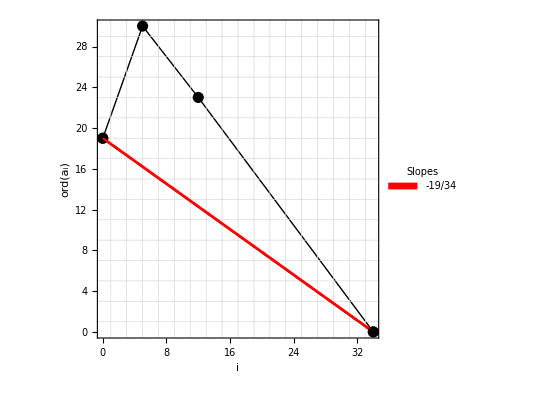

{}

{}

```mathematica
Show[$polygonFigures[[1]]]
 $pBarSave//N
$pHatSave//N
```

## Section 7: Compute infinite RH sum

```mathematica
{infRam,infiniteRHSum}=getInfiniteRHSum[$infPuiseuxSaveTable]
finiteRHSum
infiniteRHSum
```

{{{{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1}},1}},0}

140

0

## Section 8: Compute genus

```mathematica
genus=(finiteRHSum+infiniteRHSum)/2-functionDegree+1;
Print["Genus: ",genus];
```

Genus: 56

## Section 9: Generate Ramification Profile report

```mathematica
poleIndexesSave
zeroIndexesSave
(*
 if duplicate in zero and pole list, remove from the $zeroIndexes
*)
dupList=Intersection[poleIndexesSave,zeroIndexesSave];
newZeroIndexesSave=zeroIndexesSave;
If[Length@dupList>0,
newZeroIndexesSave=Complement[zeroIndexesSave,dupList];
];
newZeroIndexesSave
poleLabel="{s_p}";
zeroLabel="{s_z}";
genericLabel="{s_g}";
infLabel=infDescriptor;
labelArray={genericLabel,poleLabel,zeroLabel,infLabel};
generateRamificationReport[finiteRam,infRam,genericIndexesSave,poleIndexesSave,newZeroIndexesSave,labelArray]
```

{11,12,23,24,76}

{}

{}

Type | Cycles
{s_g}_105 | 105-(2,[13,1])
{s_p}_5 | 5-(4,5,[6,1])
{s_z}_0 | -
s_∞ | [15,1]Ramifiation Report

## Section 10: Save function to file for Maple import if available

```mathematica
Export[mapleFunctionFileName[$theTestCase],functionSave,"Text"]
```

D:\algFunctionBook\data\testCase0093\mapleFunctionName.tex

## Initialization

```mathematica
(*
 restore classic brackets [[]]
*)
SetOptions[$FrontEndSession,BoxForm`UseScriptLevelPart->False]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]]
 $HistoryLength=0;
<<ComputationalGeometry`
(*Needs["PlotLegends`"]*)
DistributeDefinitions[ConvexHull];
  $userDirectory="D:\\puiseuxSeries";
  $fNewton=Table[0,100];
  $λNewton=Table[0,100];
  $βNewton=Table[0,100];
  $cNewton=Table[0,100];
  $puiseuxSave={};
(*  $separationFactor=10;*)
  $workingPrecision=1000;
  $acf=20;
  $rcf=50;
  $charRootFactor=100;

  $useReformedFunctionFlag=True;
  $printCResidueKeyFlag=False;
  $maxPolymodalIteration=15;
  $showSegmentFlag=False;
  $stiffnessSwitchingFlag=True;
  $integrationDiagFlag1=False;
  $integrationDiagFlag2=False;
  $removeCSubResidueFactor=50;
  $mcf=50;
  $maxRootVerifyDifference=10^-50;
  $savePolygonFigures=False;
  $polygonFigures={};

  $saveRootTallyListFlag=False;
  $saveNewtonIterationDataFlag=False;
  $tallyNewtonIterationIndexFlag=False;
  $getIterationNumbersFlag=False;
  $minimalWorkingAccuracy=100;
  $thetaV=Pi/6;
  $saveFIterateFlag=False;
  $pzf=100;
  $printPolishRootFlag=False;




  $getSegmentDataFlag=False;
  $getCharRootFlag=False;
  $getPoleDataFlag=False;
  $getNewtonDataFlag=False;
  $minCharRootAccuracy=100;

DistributeDefinitions[  z,
  w,
  c,
  s,
  $workingPrecision,
  $separationFactor];

 file::fileExists="File `1` exists.";


(*$convertToNormalFormResidueFactor=10^(-50);*)
(*$removableNewtonDataResidueFactor=10^(-50);*)
(*$integrationDataResidueFactor=10^(-50);*)
$showNormalizedConstants=False;
$minNSolvePrecision=100;
```

### getSingularPoints

```mathematica
(*
 rNormArray is 1/2 distance to either nearest singular point or outer annular value
*)
(*
 $minRadiusArray is 1/3 distance to either nearest singular point or outer annular value
*)
Options[getSingularPoints]={"diag"->False,"workingPrecision"->1000};
  getSingularPoints[theFunction_,OptionsPattern[]]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDistArray,minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,zeroIndexes,originCheck,rNormArray
},
If[OptionValue["workingPrecision"]<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
If[!strictPolynomialQ[theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[theFunction],Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
}
,
at1=AbsoluteTiming[
res=Resultant[theFunction,D[theFunction,w],w];
];
If[OptionValue["diag"],
Print["Time to compute resultant: ",at1[[1]]];
];
at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->OptionValue["workingPrecision"]],Abs@#1<= Abs@#2&];
];
If[OptionValue["diag"],
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$acf)&];
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*Print["zeroIndexes: ",zeroIndexes];*)
(*
get poles
*)
poleIndexes=getPoles[theFunction,theSingularList,False];

(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDistArray=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];
minRadiusArray=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
rNormArray=MapThread[1/2Abs[#1-#2]&,{theSingularList,nearestSing}];
For[i=1,i<=Length@nearestDistArray,i++,
If[nearestDistArray[[i]]>10,
nearestDistArray[[i]]=10;
minRadiusArray[[i]]=3;
rNormArray[[i]]=5;
];
];
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray={2};
nearestDistArray={4};
rNormArray={2}
];
theReturn={theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,nearestDistArray,rNormArray};
If[OptionValue["diag"],
Print["Total singular points: ",Length@theSingularList];
Print["Precision of singular points: ",Precision@theSingularList];
Print["Total poles: ",Length@poleIndexes];
Print[Style["Pole indexes: ",Red],Style[poleIndexes,Red]];
Print["Total zero points: ",Length@zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@minRadiusArray//N];
If[Length@theSingularList>1,
Print["Smallest singular points: ",theSingularList[[1;;2]]//N];
,
Print["Singular point: ",theSingularList[[1]]//N];
];
];
];
];
];
];

theReturn
];
```

### strictPolynomialQ

```mathematica
strictPolynomialQ[myPoly_,{x_,y_}]:=Module[{levels,cList,finalList,return},
If[PolynomialQ[myPoly,{x,y}],
levels=Level[myPoly,{-1},Heads->True];
If[Length@Position[levels,x]>0 && Length@Position[levels,y]>0,
cList=Complement[levels,{Plus,Power,Times,x,y}];
finalList=Complement[cList,Select[cList,NumberQ]];
If[Length@finalList>0,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
,
return=True;
];
,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
];
,
return=False;
];
return
];
```

### getZeroIndexes

```mathematica
getZeroIndexes[theFunction_,theSingularList_,diag_:False]:=Module[{wKeys,a0Rule,a1Rule,theZeroPoints,zeroPrecision,duplicateError,zeroIndexes,theZeroList,singPrecision,difTable,maxDif,rootPrecisionTable,dif},
wKeys=CoefficientRules[theFunction,w,"NegativeLexicographic"];
a0Rule=Normal@KeyTake[wKeys,{{0},z}];
singPrecision=Floor@Precision@theSingularList;

If[Length@a0Rule>0 ,
(* found a_0 *)
If[Exponent[a0Rule[[1,2]],z]>0,
a1Rule=Normal@KeyTake[wKeys,{{1},z}];
If[Length@a1Rule>0,
(* now have a0 and a1 in function *)
If[Exponent[a1Rule[[1,2]],z]>0,
(* a1 is a poly degree>0 *)
If[a0Rule[[1,2]]===a1Rule[[1,2]],
(* at this point a0===a1 poly degree>0 so zero terms are zeros to a0 *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
,
(*Print[Style["No zero key singular points",Red]];*)
theZeroPoints={};
];
,
(* if a1 is a constant zero set is null *)
theZeroPoints={};
];
,
(* have no a1 at this point *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=a0Rule[[1,2]]/.z->#&/@ theZeroPoints;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];
zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$acf;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];
];
,
theZeroPoints={};
];
,
theZeroPoints={};
];
If[diag,
Print["theZeroPoints: ",theZeroPoints//N];
];
If[Length@theZeroPoints>0,

zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$acf;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];

zeroIndexes=Flatten[
Table[
dif=Abs[theZeroList[[i]]-#]&/@ theSingularList;
Position[dif,x_/;x==Min[dif]][[1,1]],
{i,1,Length@theZeroList}
]];
,
zeroIndexes={};

];
zeroIndexes
];
```

### getPoles

```mathematica
getPoles[theFunction_,theSingularList_,diag_:False]:=Module[{wExpList,poleFunction,pExp,singPrecision,thePoles,polePrecision,thePoleList,poleF,poleIndexes,difTable,maxDif,duplicateError,pTable,rootPrecisionTable},
wExpList=Exponent[theFunction,w,List];
poleFunction=Coefficient[theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
(* check if a_n(z) is a polynomial of degree>0 *)
singPrecision=Floor@Precision@theSingularList;
If[Last@pExp>0,
thePoles=Sort[z/.NSolve[Factor@poleFunction==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=poleFunction/.z->#&/@ thePoles;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];

polePrecision=Floor@Precision@thePoles;
duplicateError=Min[polePrecision,singPrecision]-$acf;
thePoleList=DeleteDuplicates[thePoles,Abs[#1-#2]<10^-(duplicateError)&];
,
thePoleList={};
];
poleF[a_]:=(Abs[#-a]&/@ theSingularList);
poleIndexes=Flatten[Position[poleF[#],Min[poleF[#]]]&/@ thePoleList];
poleIndexes
];
```

### getReformedFunctionTableInfinity

```mathematica
Options[getReformedFunctionTableInfinity]={"diag"->False};
 getReformedFunctionTableInfinity[theFunction_,reformedWRules_,theReformedIndexes_,OptionsPattern[]]:=Module[{functionCoeffRules,functionCoeffRulesLen,diagA,diagB,diagC,reformedFunctionTable,currentSingIndex,newWRules,wKey,keyValue,zTerms,currentReformedRule,removeIndexes,reformedKeyRule,zTermLen,reformedFunction},

functionCoeffRules=CoefficientRules[Expand[theFunction/.z->z+s],w,"NegativeLexicographic" ];
functionCoeffRulesLen=Length@functionCoeffRules;
(*Print["function coeff rules length: ",functionCoeffRulesLen];*)

If[OptionValue["diag"],
Print[Style["Creating reformedFunctionTable ...",16,Bold,Purple]];
];

reformedFunctionTable=Table[
currentSingIndex=theReformedIndexes[[rIndex]];
If[OptionValue["diag"],
Print[Style["     Processing singular index: ",Red,14,Bold],currentSingIndex];
];

If[MemberQ[theReformedIndexes,currentSingIndex],

newWRules=Table[

wKey=functionCoeffRules[[wValIndex,1]];
If[OptionValue["diag"],
Print[Style["      Processing wKey: ",Bold,Black],wKey];
];

keyValue=functionCoeffRules[[wValIndex,2]];
zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];
If[OptionValue["diag"],
Print["       zTerms: ",zTerms];
];
currentReformedRule=reformedWRules[[wValIndex]];
If[OptionValue["diag"],
Print["       Reformed rule: ",currentReformedRule];
];
removeIndexes=Select[currentReformedRule[[2]],MemberQ[#[[2]],currentSingIndex]&];

If[OptionValue["diag"] ,
Print[Style["       removeIndexes: ",Darker@Green,Bold,14],removeIndexes[[All,1]]];
Print["       kept indexes: ",Complement[Range[Length@zTerms],removeIndexes]];
];
reformedKeyRule=FromCoefficientRules[zTerms[[Complement[Range[Length@zTerms],removeIndexes[[All,1]]]]],z];
If[OptionValue["diag"],
Print[Style["       Reformed coefficient: ",Red],reformedKeyRule];
];
zTermLen=Length@zTerms;
wKey->reformedKeyRule,
{wValIndex,1,functionCoeffRulesLen}
];

reformedFunction=FromCoefficientRules[newWRules,w];
,
If[OptionValue["diag"],
Print["Using unreformed function ..."];
];
reformedFunction=theFunction;
];
{currentSingIndex,reformedFunction},
{rIndex,1,Length@theReformedIndexes}
];
reformedFunctionTable
]
```

### getReformedInfinityIndexes

```mathematica
Options[getReformedInfinityIndexes]={"diag"->False};
   getReformedInfinityIndexes[theFunction_,theSingularList_,zIndexes_,pIndexes_,OptionsPattern[]]:=Module[{diag1,diag2,diag3,singularPrecision,functionCoeffRules,functionCoeffRulesLen,reformedWRules,wKey,keyValue,zTerms,zTermLen,wp,zeroTable,zKey,zKeyValue,zeroRule,aRoots,aPrec,theZeroPos,return,removalKeys,theReformedIndexes,i,singularAccuracy,aAcc},


If[OptionValue["diag"],
Print["Function: ",polyForm[theFunction,w]];
];

singularPrecision=Floor@Precision@theSingularList;
singularPrecision=1000;
singularAccuracy=Floor@Accuracy@theSingularList;
singularAccuracy=900;

functionCoeffRules=CoefficientRules[Expand[theFunction/.z->z+s],w,"NegativeLexicographic" ];
functionCoeffRulesLen=Length@functionCoeffRules;
(*Print["function coeff rules length: ",functionCoeffRulesLen];*)

reformedWRules=Table[
(*Print["wVal term: ",functionCoeffRules[[wValIndex]]];*)
wKey=functionCoeffRules[[wValIndex,1]];

(*Print[Style["Processing wKey: ",Bold,Blue],wKey];*)
(*If[wKey=={0},
Print["Processing zero key"];
,
If[wKey=={functionDegree},
Print["Processing poles"];
];
];
*)

keyValue=functionCoeffRules[[wValIndex,2]];
zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];
zTermLen=Length@zTerms;

If[OptionValue["diag"],
Print[" zTerms: ",zTerms];
];
(*
 now check each coefficient if zero for a singualr point
*)
zeroTable=Table[
zKey=zTerms[[zIndex,1]];
zKeyValue=zTerms[[zIndex,2]];
zeroRule=Normal@KeyTake[zTerms,{zKey,s}];
If[OptionValue["diag"],
Print[Style["  Zero Rule: ",Bold],zeroRule];
];
If[!NumberQ[zeroRule[[1,2]]],
wp=Precision@zeroRule[[1,2]];
If[wp==∞,
wp=7/10 singularPrecision;
,
wp=Floor@wp;
];
If[diag1,
Print[Style["    Precision of zero rule: ",Bold],wp];
];
(*aRoots=DeleteDuplicates[s/.NSolve[SetPrecision[zeroRule[[1,2]],wp]==0,s,WorkingPrecision->wp]];*)
aRoots=DeleteDuplicates[s/.NSolve[Factor@zeroRule[[1,2]]==0,s,WorkingPrecision->wp]];

If[Floor@Accuracy@aRoots<$minimalWorkingAccuracy,
Print[Style["getReformedIndexes::roots below minimal working accuracy!",Red,Bold,12]];
Abort[];
];

aPrec=Floor@Precision@aRoots;
aAcc=Floor@Accuracy@aRoots;
If[aAcc==∞,
aAcc=singularAccuracy;
];
(*Print["aRoots precision: ",aPrec];*)

If[OptionValue["diag"],
Print[Style["    Zero rule roots: ",Bold],N[aRoots,10]];
Print[Style["    Zero rule root precision: ",Bold],aPrec];
];

theZeroPos=Sort@DeleteDuplicates[Flatten[Position[theSingularList,x_/;Abs[x-aRoots[[#]]]<10^-(aAcc-$rcf)]&/@Range[Length@aRoots]]];
(*
confirm that all zero roots are identified
*)
(*If[wKey=={0} && zIndex==1 && Length@zIndexes>0 && Length@theZeroPos!=Length@zIndexes,
Print[Style["Error: ",Red,Bold],"Found ",Length@theZeroPos," a0 points out of ",Length@zIndexes," zero indexes.  May need to increase $rcf"];
Abort[];
];*)
(*
confirm that all a_n roots are identified
*)
(*If[wKey=={functionDegree} && zIndex==1 && Length@pIndexes>0 && Length@theZeroPos!=Length@pIndexes,
Print[Style["Error: ",Red,Bold],"Found ",Length@theZeroPos," an points out of ",Length@pIndexes," pole indexes.  May need to increase $rcf"];
Abort[];
];*)

If[OptionValue["diag"],
Print[Style["theZeroPos: ",Red,14,Bold],theZeroPos];
];

If[Length@theZeroPos>0,
If[MemberQ[theZeroPos,1] && Abs[theSingularList[[1]]]<10^-100,
If[diag2,
Print["at zero"];
];
];
If[OptionValue["diag"],
Print[Style["    Singular index of zero roots: ",Red],theZeroPos];
];

return={wValIndex,wKey,zKey,zTerms,zeroRule,theZeroPos};
,
(*Print[Style["No roots of root equation are singular points",Blue]];*)
return={wValIndex,wKey,zKey,zTerms,zeroRule,{}}
];
,
(*Print[Style["No expression in s",Red]];*)
return={wValIndex,wKey,zKey,zTerms,zeroRule,{}};
];
return,
{zIndex,1,zTermLen}
];
(*
 now
*)

zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];
removalKeys={};
For[i=1,i<=Length@zeroTable,i++,
If[Length@zeroTable[[i,6]]!=0,
AppendTo[removalKeys,{i,zeroTable[[i,6]]}];
(*AppendTo[removalKeys,{i,zeroTable[[i,6]],zeroTable[[i,3]]}];*)
If[OptionValue["diag"],
Print[Style["Remove rule indexes for wKey: ",Blue,12,Bold],Style[wKey,Blue,12,Bold],Style[" coefficient index: ",Blue,12,Bold],i,": ",zeroTable[[i,6]]];
];
];
];
(*reformedKeyRule=FromCoefficientRules[zTerms[[Complement[Range[Length@zTerms],removalKeys[[All,1]]]]],z];
*)

{wKey,removalKeys},
{wValIndex,1,functionCoeffRulesLen}
];

theReformedIndexes=DeleteDuplicates@Flatten@reformedWRules[[All,2,All,2]];
{reformedWRules,theReformedIndexes}
]
```

### getReformedIndexes

```mathematica
Options[getReformedIndexes]={"diag"->False};
    getReformedIndexes[theFunction_,theSingularList_,zIndexes_,pIndexes_,compareFactor_,OptionsPattern[]]:=Module[{diag1,diag2,diag3,singularPrecision,functionCoeffRules,functionCoeffRulesLen,reformedWRules,wKey,keyValue,zTerms,zTermLen,wp,zeroTable,zKey,zKeyValue,zeroRule,aRoots,aPrec,theZeroPos,return,removalKeys,theReformedIndexes,i,singularAccuracy,aAcc,anLabel},

If[OptionValue["diag"],
Print["Function: ",polyForm[theFunction,w]];
];

singularPrecision=Floor@Precision@theSingularList;
singularAccuracy=Floor@Accuracy@theSingularList;

functionCoeffRules=CoefficientRules[Expand[theFunction/.z->z+s],w,"NegativeLexicographic" ];
functionCoeffRulesLen=Length@functionCoeffRules;
(*Print["function coeff rules length: ",functionCoeffRulesLen];*)

reformedWRules=Table[
(*Print["wVal term: ",functionCoeffRules[[wValIndex]]];*)
wKey=functionCoeffRules[[wValIndex,1]];

If[OptionValue["diag"],
Print[Style["Processing wKey: ",Bold,Blue],wKey];
];
(*If[wKey=={0},
Print["Processing zero key"];
,
If[wKey=={functionDegree},
Print["Processing poles"];
];
];
*)

keyValue=functionCoeffRules[[wValIndex,2]];
zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];
zTermLen=Length@zTerms;

If[OptionValue["diag"],
Print[" zTerms: ",zTerms];
];
(*
 now check each coefficient if zero for a singualr point
*)
zeroTable=Table[
zKey=zTerms[[zIndex,1]];
zKeyValue=zTerms[[zIndex,2]];
zeroRule=Normal@KeyTake[zTerms,{zKey,s}];
If[OptionValue["diag"],
Print[Style["  Zero Rule: ",Bold],zeroRule];
];
If[!NumberQ[zeroRule[[1,2]]],
wp=Precision@zeroRule[[1,2]];
If[wp==∞,
wp=7/10 singularPrecision;
,
wp=Floor@wp;
];
If[OptionValue["diag"],
Print[Style["    Precision of zero rule: ",Bold],wp];
];
(*aRoots=DeleteDuplicates[s/.NSolve[SetPrecision[zeroRule[[1,2]],wp]==0,s,WorkingPrecision->wp]];*)
aRoots=DeleteDuplicates[s/.NSolve[Factor@zeroRule[[1,2]]==0,s,WorkingPrecision->wp]];

If[Floor@Accuracy@aRoots<$minimalWorkingAccuracy,
Print[Style["getReformedIndexes::roots below minimal working accuracy!",Red,Bold,12]];
Abort[];
];

aPrec=Floor@Precision@aRoots;
aAcc=Floor@Accuracy@aRoots;
If[aAcc==∞,
aAcc=singularAccuracy;
];
(*Print["aRoots precision: ",aPrec];*)

If[OptionValue["diag"],
Print[Style["    Zero rule roots: ",Bold],N[aRoots,10]];
Print[Style["    Zero rule root precision: ",Bold],aPrec];
];

theZeroPos=Sort@DeleteDuplicates[Flatten[Position[theSingularList,x_/;Abs[x-aRoots[[#]]]<10^-(aAcc-compareFactor)]&/@Range[Length@aRoots]]];
(*
confirm that all zero roots are identified
*)
If[wKey=={0} && zIndex==1 && Length@zIndexes>0 && Length@theZeroPos!=Length@zIndexes,
Print[Style["Error: ",Red,Bold],"Found ",Length@theZeroPos," a0 points out of ",Length@zIndexes," zero indexes.  May need to increase compareFactor"];
(*Abort[];*)
];
(*
confirm that all a_n roots are identified
*)
If[wKey=={functionDegree} && zIndex==1 && Length@pIndexes>0 && Length@theZeroPos!=Length@pIndexes,
Print[Style["Error: ",Red,Bold],"Found ",Length@theZeroPos," an points out of ",Length@pIndexes," pole indexes.  May need to increase compareFactor"];
(*Abort[];*)
];

If[OptionValue["diag"],
Print[Style["theZeroPos: ",Red,14,Bold],theZeroPos];
];

If[Length@theZeroPos>0,
If[MemberQ[theZeroPos,1] && Abs[theSingularList[[1]]]<10^-100,
If[diag2,
Print["at zero"];
];
];
If[OptionValue["diag"],
Print[Style["    Singular index of zero roots: ",Red],theZeroPos];
];
(*Print["One or more roots of ",Subscript[anLabel, wKey[[1]]]," are singular points"];
Print["  Zero position: ",theZeroPos];*)
return={wValIndex,wKey,zKey,zTerms,zeroRule,theZeroPos};
,
anLabel="a";
(*Print["No roots of ",Subscript[anLabel, wKey[[1]]]," are singular points"];*)
return={wValIndex,wKey,zKey,zTerms,zeroRule,{}}
];
,
(*Print[Style["No expression in s",Red]];*)
return={wValIndex,wKey,zKey,zTerms,zeroRule,{}};
];
return,
{zIndex,1,zTermLen}
];
(*
 now
*)

zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];
removalKeys={};
For[i=1,i<=Length@zeroTable,i++,
If[Length@zeroTable[[i,6]]!=0,
AppendTo[removalKeys,{i,zeroTable[[i,6]]}];
(*AppendTo[removalKeys,{i,zeroTable[[i,6]],zeroTable[[i,3]]}];*)
If[diag3,
Print[Style["Remove rule indexes for wKey: ",Blue,12,Bold],Style[wKey,Blue,12,Bold],Style[" coefficient index: ",Blue,12,Bold],i,": ",zeroTable[[i,6]]];
];
];
];
(*reformedKeyRule=FromCoefficientRules[zTerms[[Complement[Range[Length@zTerms],removalKeys[[All,1]]]]],z];
*)

{wKey,removalKeys},
{wValIndex,1,functionCoeffRulesLen}
];

theReformedIndexes=DeleteDuplicates@Flatten@reformedWRules[[All,2,All,2]];
{reformedWRules,theReformedIndexes}
]
```

### getReformedFunctionTableNew

```mathematica
Options[getReformedFunctionTable]={"diag"->False};
    getReformedFunctionTable[theFunction_,reformedWRules_,theReformedIndexes_,OptionsPattern[]]:=Module[{functionCoeffRules,functionCoeffRulesLen,diagA,diagB,diagC,reformedFunctionTable,currentSingIndex,newWRules,wKey,keyValue,zTerms,currentReformedRule,removeIndexes,reformedKeyRule,zTermLen,reformedFunction},

functionCoeffRules=CoefficientRules[Expand[theFunction/.z->z+s],w,"NegativeLexicographic" ];
functionCoeffRulesLen=Length@functionCoeffRules;
(*Print["function coeff rules length: ",functionCoeffRulesLen];*)
If[OptionValue["diag"],
Print[Style["Creating reformedFunctionTable ...",16,Bold,Purple]];
];

reformedFunctionTable=Table[
currentSingIndex=theReformedIndexes[[rIndex]];
If[OptionValue["diag"],
Print[Style["     Processing singular index: ",Red,14,Bold],currentSingIndex];
];

If[MemberQ[theReformedIndexes,currentSingIndex],

newWRules=Table[

wKey=functionCoeffRules[[wValIndex,1]];
If[OptionValue["diag"],
Print[Style["      Processing wKey: ",Bold,Black],wKey];
];

keyValue=functionCoeffRules[[wValIndex,2]];
zTerms=CoefficientRules[keyValue,z,"NegativeLexicographic" ];
If[OptionValue["diag"],
Print["       zTerms: ",zTerms];
];
currentReformedRule=reformedWRules[[wValIndex]];
If[OptionValue["diag"],
Print["       Reformed rule: ",currentReformedRule];
];
removeIndexes=Select[currentReformedRule[[2]],MemberQ[#[[2]],currentSingIndex]&];

If[OptionValue["diag"] ,
Print[Style["       removeIndexes: ",Darker@Green,Bold,14],removeIndexes[[All,1]]];
Print["       kept indexes: ",Complement[Range[Length@zTerms],removeIndexes]];
];
reformedKeyRule=FromCoefficientRules[zTerms[[Complement[Range[Length@zTerms],removeIndexes[[All,1]]]]],z];
If[OptionValue["diag"],
Print[Style["       Reformed coefficient: ",Red],reformedKeyRule];
];
zTermLen=Length@zTerms;
wKey->reformedKeyRule,
{wValIndex,1,functionCoeffRulesLen}
];

reformedFunction=FromCoefficientRules[newWRules,w];
,
If[OptionValue["diag"],
Print["Using unreformed function ..."];
];
reformedFunction=theFunction;
];
{currentSingIndex,reformedFunction},
{rIndex,1,Length@theReformedIndexes}
];
reformedFunctionTable
]
```

### polyForm(poly,var)

```mathematica
polyForm[poly_,var_]:=Module[{coeffs=CoefficientRules[poly,var]//Sort},Interpretation[Row[Table[Row[{"(",coeff[[2]],")",var^coeff[[1,1]]/.1->""}],{coeff,coeffs}],"+"],poly]]
```

### getSingularRange

```mathematica
getSingularRange[y_,z_,theSingularList_]:=Module[{return},
If[y===-1,
return=Range[1,Length@theSingularList];
,
If[Length@y>0,
return=y;
,
If[z==-1,
return={y};
,
return=Range[y,z];
];
];
];
return
];
```

### getMinValidExp

```mathematica
getMinValidExp[singIndex_,theSingularList_]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[$theFunction/.z->(z+theSingularList[[singIndex]])];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];

getMinValidExpForGenus[singIndex_,theSingularList_]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[$theFunction/.z->(z+theSingularList[[singIndex]])];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];


getMinValidExpInf[]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[$theFunction];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];

getMinValidTransFunction[f_]:=Module[{tFunction,cList,minValidCoeff},

tFunction=Expand[f];
cList=CoefficientList[tFunction,w];
minValidCoeff=Min@((Min@Abs@CoefficientList[#,z]//N)&/@ cList);
MantissaExponent[minValidCoeff][[2]]
];
```

### ConvertToNormalForm

```mathematica
convertToNormalFormNew[theF_]:=Module[{wRules,theWKeys,theATerms,aTermOrders,wPowers,orderArray,deletedOrderArray,normalEqn,normalConstraints,minData,thepoly,currentmu,mylambda},
  wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
theWKeys=Keys[wRules];
theATerms=Values[wRules];
aTermOrders=Min@#&/@(Exponent[#,z,List]&/@ theATerms);
wPowers=Flatten[theWKeys];
orderArray=MapThread[{#1,#2}&,{aTermOrders,wPowers}];

deletedOrderArray=DeleteCases[orderArray,{_,0}];
normalEqn=μ+deletedOrderArray[[-1,1]]==functionDegree λ;
normalConstraints=Table[
μ+deletedOrderArray[[i,1]]>=deletedOrderArray[[i,2]] λ,
{i,1,Length@deletedOrderArray-1}
];

minData=Minimize[{λ,normalEqn &&(And@@normalConstraints)&& Element[{μ,λ},PositiveIntegers]},{μ,λ}];
{currentmu,mylambda}={μ,λ}/.minData[[2]];
Print["currentmu: ",currentmu];
Print["mylambda: ",mylambda];
thepoly=Expand[z^currentmu(theF/.w->w/(z^mylambda))];
Print["normal poly: ",thepoly//N];
{thepoly,mylambda,currentmu}
];
```

```mathematica
convertToNormalForm[theF_]:=Module[{wRules,wKeys,zRules,theOrders,positiveOrders,fDegree,normalEqn,normalConstraints,eqnA,i,minData,currentmu,mylambda,thepoly,μ,λ,lVal,mVal},

 wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
wKeys=wRules[[All,1]];
zRules={#[[1,1]],CoefficientRules[#[[2]],z,"NegativeLexicographic"]}&/@ wRules;
theOrders={#[[1]],#[[2,1,1,1]]}&/@ zRules;
positiveOrders=Select[theOrders,#[[1]]>0&];
fDegree=Max@Exponent[theF,w,List];
normalEqn=μ+positiveOrders[[-1,2]]==fDegree λ;
normalConstraints=Table[
eqnA=μ+positiveOrders[[i,2]]>=positiveOrders[[i,1]] λ;
eqnA,
{i,1,Length[positiveOrders]-1}
];

minData=Minimize[{λ,normalEqn &&(And@@normalConstraints)&& Element[{μ,λ},PositiveIntegers]},{μ,λ}];
{currentmu,mylambda}={μ,λ}/.minData[[2]];
thepoly=Expand[z^currentmu(theF/.w->w/(z^mylambda))];
If[$showNormalizedConstants,
Print["mu and lambda from Minimize function: "];
Print["mylambda: ",mylambda];
Print["currentmu: ",currentmu];
];
{thepoly,mylambda,currentmu}
];

convertToNormalForm2[theF_]:=Module[{wRules,wKeys,zRules,theOrders,positiveOrders,fDegree,normalEqn,normalConstraints,eqnA,i,minData,currentmu,mylambda,thepoly,μ,λ,lVal,mVal},

 wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
wKeys=wRules[[All,1]];
zRules={#[[1,1]],CoefficientRules[#[[2]],z,"NegativeLexicographic"]}&/@ wRules;
theOrders={#[[1]],#[[2,1,1,1]]}&/@ zRules;
positiveOrders=Select[theOrders,#[[1]]>0&];
fDegree=Max@Exponent[theF,w,List];
normalEqn=μ+positiveOrders[[-1,2]]==fDegree λ;
normalConstraints=Table[
eqnA=μ+positiveOrders[[i,2]]>=positiveOrders[[i,1]] λ;
eqnA,
{i,1,Length[positiveOrders]-1}
];

minData=Minimize[{λ,normalEqn &&(And@@normalConstraints)&& Element[{μ,λ},PositiveIntegers]},{μ,λ}];
{currentmu,mylambda}={μ,λ}/.minData[[2]];
thepoly=Expand[z^currentmu(theF/.w->w/(z^mylambda))];
If[$showNormalizedConstants,
Print["mu and lambda from Minimize function: "];
Print["mylambda: ",mylambda];
Print["currentmu: ",currentmu];
];
{thepoly,mylambda,currentmu}
];
```

### getNormalVals using Max[ord(an)-ord(ai)/(n-1)]

```mathematica
getNormalVals[theFunction_]:=Module[{wExp,functionDegree,wCoef,orderList,theLambda,theMu,lambdaList,theReturn},
wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp;
wCoef=CoefficientRules[theFunction,w,"NegativeLexicographic"];
If[Length@wCoef<3,
Print[Style["Function needs more than three terms to use getNormalVals!",Red,Bold]];
theReturn={-1,-1};
,
orderList={#[[1,1]],Exponent[#[[2]],z,List]//First}&/@ wCoef;
(*Print["orderList: ",orderList[[2;;-2]]];*)
lambdaList=((orderList[[-1,2]]-#[[2]])/(orderList[[-1,1]]-#[[1]])&/@ orderList[[2;;-2]]);
Print["Lambda list: ",lambdaList];
theLambda=Max[Ceiling@lambdaList];
theMu=theLambda functionDegree-orderList[[-1,2]];
theReturn={theLambda,theMu};
];
theReturn
]
```

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];

aForm2[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[c]@*thecRules[c]]@toPowerBoxes[z]@thecRules[z][f];
```

### getNewtonData

```mathematica
getNewtonData[thef_,theK_,normalExp_,theSingularList_]:=Module[{j,rootnum,theftemp,theclist,expList,minVals,lcpsave,myPoints,pgp,sg,newtonLeg,mylines,maxx,maxy,slopeInterceptList,theCEquations,theRootTally,rootstatus,theSegmentData,mysegments,currentRootTally,currentSegment,currentRootList,theT,theD,mycurrentw,multinum,myS,charRoots,theLegArray,thePolygonPoints,theRotatedPoints,hullIndexes,cZeroList,cRemovalF},

theftemp=thef;

theclist=CoefficientList[theftemp,w];
expList=Exponent[theclist,z,Min];
minVals=MapThread[Coefficient[#1,z,#2]&,{theclist,expList}];
 {theLegArray,thePolygonPoints,theRotatedPoints}=getSegmentData[Expand@thef,theK];
If[$getNewtonDataFlag,
Print["theLegArray: ",theLegArray//N];
Print["thePolygonPoints: ",thePolygonPoints//N];
];


If[Length[theLegArray]>0,
{
{slopeInterceptList,theRootTally}=getCharRoots[theLegArray,thePolygonPoints,theRotatedPoints,theSingularList];
If[$getNewtonDataFlag,
Print["slopeInterceptList: ",slopeInterceptList//N];
Print["root tally: ",theRootTally//N];
];

(* keep copy of theRootTally to detect multiple factors of a finite series *)
currentRootTally=theRootTally;
theSegmentData=MapThread[{#1,#2}&,{slopeInterceptList,theRootTally}];
Clear[x];


mysegments=Range[Length[theSegmentData]];

 Do[ 
{
$fNewton[[theK]]=theftemp;
currentSegment=theSegmentData[[segmentnum]];
currentRootList=currentSegment[[2]];
If[$getNewtonDataFlag,
Print["current root list size: ",Length@currentRootList];
];

{$λNewton[[theK]],$βNewton[[theK]]}=currentSegment[[1]];
For[rootnum=1,rootnum≤Length[currentRootList],rootnum++,
$cNewton[[theK]]=currentRootList[[rootnum,1]];

If[currentRootList[[rootnum,2]]≠1,
(* generate next polygon leg *)
{

If[$getNewtonDataFlag,
Print["$fNewton[[theK+1]] before remove residues: ",N[polyForm[1/z^($βNewton[[theK]])$fNewton[[theK]]/.w->z^($λNewton[[theK]])($cNewton[[theK]]+w),w],10]];
];
{cZeroList,cRemovalF}=identifyPolygonZeros[1/z^($βNewton[[theK]])$fNewton[[theK]]/.w->z^($λNewton[[theK]])(c+w),$cNewton[[theK]]];

$fNewton[[theK+1]]=cRemovalF;

If[$getNewtonDataFlag,
Print["$fNewton[[theK+1]] after removeCResidues: ",polyForm[N[$fNewton[[theK+1]],10],w]];
];

If[(theK+1)>1 && $getSegmentDataFlag,
Print[Style["Entering polygon iteration ",Purple,Bold,20,Underlined],Style[theK+1,Purple,Bold,20]];
Print["  for root: ",$cNewton[[theK]]//N];
];
getNewtonData[$fNewton[[theK+1]],theK+1,normalExp,theSingularList];

}
,

{

If[$getNewtonDataFlag,
Print["Adding segment term for root ",currentRootList[[rootnum,1]]//N];
];
theT=theK;
theD=getCommonDenom[theK,$λNewton];

mycurrentw=currentRootList[[rootnum,1]];
charRoots=Table[$cNewton[[i]],{i,1,theK}];

AppendTo[$puiseuxSave,{theK,charRoots,theD,Table[$λNewton[[j]],{j,1,theK}],$fNewton[[theT]],$βNewton[[theT]],mycurrentw,normalExp}];

}
];
];
},
{segmentnum,mysegments}
];
}
];
];
```

### getSegmentData

```mathematica
getSegmentData[theF_,theK_]:=Module[{wRules,zRules,polygonPoints,maxX,maxY,hullIndexes,hullPoints,hullMin,minPos, lowLegFound,index,lowLegPoints,currentX,nextX,currentY,slope,yIntercept,polygonPointsG,convexHullG,hullPointsG,rotatedPoints,legArray,currentLeg,legIndex,totalPts,colorArray,finalLegIndexes,finalLegPoints,legIndexes, finalLegPointsG,lineG , dashPlots,pData,pPoint,pSlope,theY,xStop ,subReturn,linePoints,slopeLegendData,slopeColorData,thePlotLegend,legendPlot,xGridF,yGridF,tableData,wCoef},
(*
 requires function to be normalized
*)

 If[$getSegmentDataFlag,
If[theK==1,
Print["f: ",aForm[theFunction]];
];
Print["f_n: ",aForm[N[theF,4]]];
wCoef=CoefficientRules[theF,w,"NegativeLexicographic"]//N;
tableData={#[[1]],#[[2]]}&/@ wCoef;
Print[Grid[tableData,Alignment->Left]];
];
(*
 get Newton polygon and lower Newton legs
*) 
wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
zRules=getCoefficientRules[#]&/@ wRules[[All,2]];
(*zRules=CoefficientRules[#,z,"NegativeLexicographic"]&/@ wRules[[All,2]];*)
If[$getSegmentDataFlag,
Print["theF: ",theF//N];
AppendTo[tempFunSave,theF];
Print["wRules: ",wRules//N//MatrixForm];
Print["zRules: ",zRules//N//MatrixForm];
]; 
(*
for each coefficient of z, save {power of w, power of z, coefficient of z } in polygonPoints
*) 
polygonPoints=MapThread[{#1[[1,1]],#2[[1,1,1]],#2[[1,2]]}&,{wRules,zRules}];
If[$getSegmentDataFlag,
Print[Style["polygonPoints after MapThread: ",Red],polygonPoints//N];
];
maxX=Max@polygonPoints[[All,1]];
maxY=Max@polygonPoints[[All,2]];
(* now compute the convex hull of polygonPoints *) 
(* note:  can also use more updated convexHullMesh but timing is equivalent: 
d=RandomReal[{0,1},{20,2}];
   hull=ConvexHullMesh[d];
  order=MeshCells[hull,2][[1,1]];
   *) 
hullIndexes=ConvexHull[polygonPoints[[All,{1,2}]]];
hullPoints=polygonPoints[[hullIndexes]];

If[$getSegmentDataFlag || $savePolygonFigures,
Print[Style["First hull plot",16,Red]];
polygonPointsG=Graphics@{PointSize[0.01],Black,Point@polygonPoints[[All,{1,2}]]};
convexHullG=Graphics@{Line@Append[polygonPoints[[hullIndexes,{1,2}]],polygonPoints[[hullIndexes[[1]],{1,2}]]]};
hullPointsG=Graphics@{PointSize[0.02],Black,Point@hullPoints[[All,{1,2}]]};
(*Print[Show[{polygonPointsG,convexHullG,hullPointsG},Axes->True,AxesOrigin->{0,0},GridLines->{Table[i,{i,0,maxX}],Table[i,{i,0,maxY}]},AspectRatio->1,PlotRange->{{0,maxX},{0,maxY}},PlotLabel->Style["Newton Polygon",16,Black]]]*)
];
(*
 arrange the convex hull points beginning with the point with minimum power of w.  Since the function
is normalized, there will be a {n,0} final term of points guaranteeing at least one lower newton leg
*) 
hullMin=Min@hullPoints[[All,1]];
minPos=Position[hullPoints,{hullMin,_,_}][[1,1]];
rotatedPoints=RotateLeft[hullPoints,minPos-1];
(* now the convex hull is in order of smallest w-degree *)
If[$getSegmentDataFlag,
Print["hullPoints: ",hullPoints//N];
Print["rotated points: ",rotatedPoints//N];
Print[Style["Final polygon points G: ",Purple],rotatedPoints//N];
];
(*
 now get the lower legs of the convex hull
*)
lowLegFound=False;
index=0;
lowLegPoints={};

While[!lowLegFound && index<(Length@rotatedPoints)-1,
index++;
currentX=rotatedPoints[[index,1]];
nextX=rotatedPoints[[index+1,1]];
currentY=rotatedPoints[[index,2]];
slope=(rotatedPoints[[index+1,2]]-rotatedPoints[[index,2]])/(rotatedPoints[[index+1,1]]-rotatedPoints[[index,1]]);
(*If[$showSegmentFlag,
Print[Style["the slope: ",Red],slope//N];
];*)
yIntercept=currentY-slope currentX;
If[nextX<currentX,
lowLegFound=True;
,
If[slope<0,
(*If[$showSegmentFlag,
Print[Style["rotated points: ",Darker@Green],rotatedPoints//N];
Print[Style["Appending to logLegPoints: ",Darker@Green],{index,index+1}];
];*)
AppendTo[lowLegPoints,{index,index+1,-slope,yIntercept}];
,
If[slope==0 && theK==1,
If[$getSegmentDataFlag,
Print[Style["Appending to lowLegPoints at k=1",Magenta,Bold]];
];
AppendTo[lowLegPoints,{index,index+1,-slope,yIntercept}];
,
lowLegFound=True;
];
];
];
];
If[maxY==0,
maxY=10;
];
(*
at this point lowLegPoints have {index1,index2,neg slope, y-intercept} of all points on lower legs 
with index1 and index2 indexes into rotatedPoints
*) 

If[Length@lowLegPoints==0,
Print[Style["Did not find any lower Newton legs! Function is not normalized. Stopping.",Red,Bold,14]];
subReturn={lowLegPoints,polygonPoints,rotatedPoints};
,
If[$getSegmentDataFlag,
Print[Style["lowLegPoints: ",Red],lowLegPoints//N];
];
(*
 now using lower leg slopes, assign points in the lower leg indexes to each leg 
*)
totalPts=Length@lowLegPoints;
legIndex=1;

currentLeg={lowLegPoints[[1]]};
legArray={};
If[Length@lowLegPoints==1,
legArray={currentLeg};
,
While[legIndex<totalPts,
legIndex++;
If[lowLegPoints[[legIndex,3]]==currentLeg[[1,3]],
AppendTo[currentLeg,lowLegPoints[[legIndex]]];
If[legIndex==totalPts,
AppendTo[legArray,currentLeg];
];
,
AppendTo[legArray,currentLeg];
currentLeg={lowLegPoints[[legIndex]]};
If[legIndex==totalPts,
AppendTo[legArray,currentLeg];
];
];
];
];
(*
legArray now has {{pt1,pt2,pt3},{pt4,pt5},{pt6},{pt7,pt8,pt9,pt10}}
with each list {pt1,pt2,...,ptn} representing the points {pt1,pt2,...,ptn} assigned to each lower leg
*) 
If[$getSegmentDataFlag,
Print["legArray: ",legArray];
];
(*
generate diagrams if $showSegmentFlag is set
*)
If[$getSegmentDataFlag || $savePolygonFigures,
If[Length@legArray==1,
finalLegIndexes=DeleteDuplicates@Flatten@legArray[[1,All,{1,2}]];
finalLegPoints=rotatedPoints[[#,{1,2}]]&/@ finalLegIndexes;
,
finalLegIndexes=Table[
If[$getSegmentDataFlag,
Print["processing leg array: ",legArray[[legIndex]]//N];
];
legIndexes=DeleteDuplicates[Flatten@legArray[[legIndex,All,{1,2}]]];
If[$getSegmentDataFlag,
Print["    leg points for this leg array: ",legIndexes];
];
legIndexes,
{legIndex,1,Length@legArray}];
finalLegPoints=rotatedPoints[[#,{1,2}]]&/@ finalLegIndexes;
];
If[$getSegmentDataFlag,
Print["final leg point array: ",finalLegPoints];
];
colorArray={Red,Blue,Darker@Yellow,Darker@Green,Magenta,Brown,Purple,Pink,Brown};
(*
 generate slope legends
*)
slopeLegendData=-legArray[[All,1,3]];
slopeColorData=colorArray[[1;;Length@legArray]];
(*thePlotLegend=Placed[SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]],{0.8,0.8}];
*)
thePlotLegend=SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]];

If[Length@legArray==1,
finalLegPointsG=Graphics@{Red,PointSize[0.02],Point@(finalLegPoints[[All,{1,2}]])};
lineG=Graphics@{Thickness[0.005],Red,Line@finalLegPoints[[All,{1,2}]]};
,
linePoints={#[[1]],#[[-1]]}&/@ finalLegPoints;
If[Length@linePoints>Length@colorArray,
Print[Style["Number of lower legs exceed number of colors in colorArray!",16,Bold,Red]];
];
finalLegPointsG=Graphics@{Red,PointSize[0.02],Point@(DeleteDuplicates[Flatten[finalLegPoints[[All,{1,2}]],1]])};
(*lineG=MapThread[(Graphics@{Thickness[0.005],#1,Line@#2})&,{colorArray[[1;;Length@finalLegPoints]],finalLegPoints[[All,{1,2}]]}];*)
lineG=MapThread[(Graphics@{Thickness[0.0075],#1,Line@#2})&,{colorArray[[1;;Length@finalLegPoints]],linePoints}];
];
 (*
 routine to generate dashed blue lines:  dashPlots,pData,pPoint,pSlope,theY,xStop
*)
(*Print[Style["preparing to generate dashed lines",Red]];
Print[Style["     Leg array: ",Red],legArray//N];
*)
dashPlots=Table[
If[Length@legArray==1,
pData=legArray[[1,1]];
pPoint=finalLegPoints[[1]];
pSlope=-legArray[[1,1,3]];
,
pData=legArray[[lineIndex,1]];
pPoint=finalLegPoints[[lineIndex,1]];
pSlope=-pData[[3]];
];

If[pSlope!=0,
theY[x_]=pSlope(x-pPoint[[1]])+pPoint[[2]];
xStop=x/.Solve[theY[x]==0,x][[1]];
,
theY[x_]=pPoint[[2]];
xStop=maxX;
];

Plot[theY[x],{x,0,xStop},PlotStyle->{Dashed,colorArray[[lineIndex]]}],
{lineIndex,1,Length@legArray}
];
If[$savePolygonFigures,
thePlotLegend=Placed[SwatchLegend[slopeColorData,slopeLegendData,LegendLabel->Style["Slopes",Bold,Black]],{0.8,0.6}];
];
legendPlot=Plot[0,{x,0,10^-4},PlotLegends->thePlotLegend];
xGridF[x_]:=Piecewise[{{Table[a,{a,10,x,10}],x>100},{Table[a,{a,5,x,5}],x>50},{Table[a,{a,1,x,2}],x>10}}];
yGridF[x_]:=Piecewise[{{Table[a,{a,10,x,10}],x>100},{Table[a,{a,5,x,5}],x>50},{Table[a,{a,1,x,2}],x>10}}];


Print[Show[{convexHullG,finalLegPointsG,lineG,polygonPointsG,hullPointsG,dashPlots,legendPlot},Axes->True,GridLines->{xGridF[maxX],yGridF[maxY]},(*GridLines->{Table[i,{i,0,maxX}],Table[i,{i,0,maxY}]},*)AspectRatio->1,PlotRange->{{0,maxX},{0,maxY}},FrameLabel->{Style["i",14,Bold,Black],Rotate[Style["ord(a_i)",14,Bold,Black],-90 Degree]},Frame->{{True,False},{True,False}}(*,PlotLabel->Row[{Style[Subscript[f, theK],14,Bold,Black],Style[" Newton Polygon",14,Bold,Black]}]*)]];
If[$savePolygonFigures,
Print["Saving polygons to $polygonFigures"];
AppendTo[$polygonFigures,Show[{convexHullG,finalLegPointsG,lineG,polygonPointsG,hullPointsG,dashPlots,legendPlot},Axes->True,GridLines->{xGridF[maxX],yGridF[maxY]},AspectRatio->1,PlotRange->{{0,maxX},{0,maxY}},FrameLabel->{Style["i",14,Bold,Black],Rotate[Style["ord(a_i)",14,Bold,Black],-90 Degree]},Frame->{{True,False},{True,False}}]];
];

];

subReturn={legArray,polygonPoints,rotatedPoints};
];
If[$getSegmentDataFlag,
Print[Style["subReturn in getSegmentData: ",Blue],subReturn//N];
];

subReturn

 ];
```

### getCoefficientRules

```mathematica
getCoefficientRules[a_]:=Module[{expList,coefList},
expList=Exponent[a,z,List];
coefList=Coefficient[a,z,#]&/@ expList;
Table[{expList[[i]]}->coefList[[i]],{i,1,Length@expList}]
]
SetAttributes[getCoefficientRules,Listable];
```

### getCharRoots

```mathematica
getCharRoots[theLegArray_,thePolygonPoints_,theRotatedPoints_,theSingularList_]:=Module[{charEqns,pointIndexes,charRootList,rootAcc,nonZeroRootList,rootTallyList,slopeInterceptList,charEqnsPrecision,netTolerance,wp,attempts,charRootPrecision,difTable,charEqnsAccuracy,charRootAccuracy,newRootTallyList},
If[$getCharRootFlag,
Print[Style["Entering getCharRoots",Red,14,Bold]];
Print["     theLegArray: ",theLegArray//N];
];
If[$getCharRootFlag,
Print[Style["thePolygonPoints G= ",Black,Bold],thePolygonPoints//N];
Print[Style["characteristic points C= ",Black,Bold],{#[[3]]//N,#[[1]]}&/@ theRotatedPoints];
];

charEqns=Table[
If[Length@theLegArray[[legIndex]]==1,
pointIndexes=theLegArray[[legIndex,1,{1,2}]];
,
pointIndexes=DeleteDuplicates@Flatten@theLegArray[[legIndex,All,{1,2}]];
If[$getCharRootFlag,
Print["       Deleted duplicates: ",pointIndexes];
];
];
If[$getCharRootFlag,
Print[Style["pointIndexes: ",Purple,Bold],pointIndexes//N];
];

Plus@@Table[
theRotatedPoints[[pointIndexes[[pIndex]],3]] x^theRotatedPoints[[pointIndexes[[pIndex]],1]],
{pIndex,Length@pointIndexes}
],
{legIndex,1,Length@theLegArray}
];

charEqnsPrecision=Floor@Precision@charEqns;
charEqnsAccuracy=Floor@Accuracy@charEqns;

If[$getCharRootFlag,
Print[Style["char eqns: ",Purple,Bold,14],charEqns//N];
Print["charEqnsPrecision: ",charEqnsPrecision];
];
(*If[charEqnsPrecision==∞ ,
charEqnsPrecision=Floor@Precision@theSingularList;
If[$getCharRootFlag,
Print["Reducing infinite precision of char eqns to ",charEqnsPrecision];
];
charEqns=SetPrecision[charEqns,charEqnsPrecision];
];*)
(* ***************************** *)
If[charEqnsPrecision==∞,
charEqnsPrecision=Floor@Precision@theSingularList;
If[charEqnsPrecision==∞,
charEqnsPrecision=900;
];
If[$getCharRootFlag,
Print["Reducing infinite precision of char eqns to ",charEqnsPrecision];
];
charEqns=SetPrecision[charEqns,charEqnsPrecision];
charRootList=Quiet[(x/.NSolve[#,x,WorkingPrecision->charEqnsPrecision])&/@ charEqns];
charRootPrecision=Floor@Precision@charRootList;
charRootAccuracy=Floor@Accuracy@charRootList;

(*
 now verify root to desired accuracy
*)
difTable=Table[
Abs[(charEqns[[i]]/.x->#)]&/@ charRootList[[i]],
{i,1,Length@charEqns}
];
If[$getCharRootFlag,
Print[Style["     current char root precision: ",Blue],charRootPrecision];
If[Max@(difTable//Flatten)>10^-(charRootAccuracy-$charRootFactor),
Print[Style["Root verify precision failed: ",Red],N[difTable,10]];
,
Print[Style["Char root verify passed",Blue]];
Print["difTable: ",N[difTable,10]];
];
];
,
(* 
char root precision not infinity, adjust wp until root precision is near char equation precision
*)
charRootList=Quiet[(x/.NSolve[#,x])&/@ charEqns];
charRootPrecision=Floor@Precision@charRootList;
charRootAccuracy=Floor@Accuracy@charRootList;

(*
 now verify root to desired accuracy
*)
difTable=Table[
Abs[(charEqns[[i]]/.x->#)]&/@ charRootList[[i]],
{i,1,Length@charEqns}
];
If[$getCharRootFlag,
Print[Style["     current char root precision: ",Blue],charRootPrecision];
If[Max@(difTable//Flatten)>10^-(charRootAccuracy-$charRootFactor),
Print["char root accuracy: ",charRootAccuracy];
Print["$charRootFactor: ",$charRootFactor];
Print[Style["Root verify precision failed: ",Red],N[difTable,10]];
,
Print[Style["Char root verify passed",Blue]];
Print["difTable: ",N[difTable,10]];
];
];
];
(*       *************************** *)
If[$getCharRootFlag,
Print[Style["     Final char root precision: ",Black,Bold,12],Precision@charRootList];
];
AppendTo[charEqnsSave,{charEqns,charRootList}];
rootAcc=Floor@Accuracy@charRootList;
If[rootAcc<$minCharRootAccuracy,
Print["Characteristic equation accuracy: ",rootAcc," is less than ",$minCharRootAccuracy];
Print[Style["Increase working precision.",Red]];
];
netTolerance=rootAcc-$acf;

If[$getCharRootFlag,
Print["char equation to nsolve: ",charEqns//N];
Print["Length of char roots: ",Length@#&/@ charRootList];
Print["charRootList: ",N[charRootList,10]];
Print["rootAcc: ",rootAcc];
Print["tolerance: ",netTolerance];
];
(*If[netTolerance<$minCharRootAccuracy,
Print[Style["Char roots accuracy below $minCharRootAccuracy!  Accuracy: ",Red,Bold],netTolerance];
Print[Style["Increase working precision of singular points!",Red,Bold]];
Abort[];
];
*)
nonZeroRootList=Select[#,Abs[#]>10^(-(netTolerance))&]&/@ charRootList;
If[$getCharRootFlag,
Print["nonZeroRootList: ",N[nonZeroRootList,10]];
];
rootTallyList=Tally[#,Abs[#1-#2]<10^(-Ceiling[netTolerance])&]& /@ nonZeroRootList;
If[$getCharRootFlag,
Print["rootTallyList: ",N[rootTallyList,10]];
];
(*
 now polish root tally if multiple roots
*)


newRootTallyList=polishCharRoots[charEqns,rootTallyList];
If[$getCharRootFlag,
Print["newRootTallyList: ",N[newRootTallyList,10]];
];
If[$printPolishRootFlag,
Print[Style["old root tally list: ",Blue],rootTallyList//N];
Print[Style["new root tally list: ",Blue],newRootTallyList//N];
Print["Current equation and tallies: "];
Print["     charEqns: ",charEqns//N];
Print["     rootTallyList: ",rootTallyList//N];
];

If[$saveRootTallyListFlag,
AppendTo[$rootTally,{nonZeroRootList,rootTallyList}];
AppendTo[$multipleRootCheck,{charEqns,rootTallyList}];
];
If[$getCharRootFlag,
Print["nonZeroRootList: ",nonZeroRootList//N];
Print["rootTallyList: ",rootTallyList//N];
];
(* 
negate slopes here
*)
If[Length@theLegArray==1,
slopeInterceptList={theLegArray[[1,1,{3,4}]]};
,
slopeInterceptList={#[[1]],#[[2]]}&/@ theLegArray[[All,1,{3,4}]];
];
If[$getCharRootFlag,
Print[Style["Exiting getCharRoots",Red]];
];
{slopeInterceptList,newRootTallyList}
];
```

### polishCharRoots

```mathematica
polishCharRoots[eqnArray_,tallyArray_]:=Module[{theTally,newRootArray,tally,currentTallyData,root,currentTally,multiplicity, newX,tallyRootAcc,rootPos,newRoot,netArray,rootPosArray,multiRootPrec,rootTallyPrec,difTable,altPos,altPosArray},
theTally=MapThread[{#1,#2}&,{eqnArray,tallyArray}];

netArray={};
For[tally=1,tally<=Length@theTally,tally++,
currentTallyData=theTally[[tally]];
If[$printPolishRootFlag,
Print["polishCharRoot: currentTallyData: ",currentTallyData//N];
];
newRootArray={};
For[root=1,root<=Length@currentTallyData[[2]],root++,
currentTally=currentTallyData[[2,root]];
If[$printPolishRootFlag,
Print["polishCharRoot: currentTally: ",currentTally//N];
];
multiplicity=currentTally[[2]];
If[currentTally[[2]]>1,
If[$printPolishRootFlag,
Print["     currentTally: ",N[currentTally,10]];
Print[Style["Detected multiple roots: ",Red],currentTally//N];
Print["     tally eqn: ",currentTallyData[[1]]//N];
Print["     tally eqn prec: ",Precision@currentTallyData[[1]]];
Print["     tally root: ",currentTally[[1]]//N];
Print["     tally root prec: ",Precision@currentTally[[1]]];
Print["     multiplicity: ",multiplicity];
Print["     Running derivative root eqn: "];
Print["     Precision of derivative equation: ",Precision@D[currentTallyData[[1]],{x,multiplicity-1}]];
];
multiRootPrec=Floor@Precision@currentTallyData[[1]];
(*Print[Style["multiRoot equation Prec: ",Red],multiRootPrec];*)
newX=x/.NSolve[D[currentTallyData[[1]],{x,multiplicity-1}]==0,x(*,WorkingPrecision->(multiRootPrec)*)];
If[$printPolishRootFlag,
Print["Roots from derivative NSolve: ",newX//N];
Print["Precision of roots from derivative NSolve: ",Precision@#&/@ newX];
];
(*
find tally root in newX: newX,tallyRootAcc,rootPos,newRoot
*)
tallyRootAcc=Floor@Accuracy@currentTally[[1]];
rootTallyPrec=Min@{Floor@Precision@currentTally[[1]],Floor@Precision@newX};
(*Print[Style["rootTallyPrec: ",Red],rootTallyPrec];*)
difTable=Abs[#-currentTally[[1]]]&/@ newX;
(*Print[Style["multi root difTable: ",Red],N[difTable,10]];*)
altPosArray=Position[difTable,Min[difTable]];
(*Print[Style["alt root pos: ",Red],altPos];
Print[Style["     altRoot: ",Red],N[newX[[altPos]],10]];
*)
(*rootPosArray=Position[newX,x_/;Abs[x-currentTally[[1]]]<10^-(rootTallyPrec-50)];*)
If[Length@altPosArray==0,
Print[Style["polishCharRoot: Position error!",12,Red]];
Print["altPos: ",altPosArray];
Abort[];
];
(*rootPos=rootPosArray[[1,1]];
*)
altPos=altPosArray[[1,1]];
If[$printPolishRootFlag,
Print["tallyRootAcc: ",tallyRootAcc];
Print["root dif: ",N[Abs[newX-currentTally[[1]]],20]];
Print["     root position: ",altPos];
Print["     newX vals: ",newX[[altPos]]//N];
Print["     Prec of newX vals: ",Precision@newX[[altPos]]];
];
(*
 now replace root with higher-precision version
*)
(*newRoot=newX[[rootPos]];*)
newRoot=newX[[altPos]];
,
newRoot=currentTally[[1]];
];
AppendTo[newRootArray,{newRoot,multiplicity}];
];
AppendTo[netArray,newRootArray];
];
netArray
];
```

### identifyPolygonZeros

```mathematica
identifyPolygonZeros[f_,cVal_]:=Module[{f2,wTerms,theCTerms,cTermVals,theZeroList,cTemp,cKey,cKeyValue,i,j,adjustedTolerance,zeroTermList,posList,newF,zeroTermListExp,toleranceLimit,minExpList,zList,zListExp},

If[$saveFIterateFlag,
Print["     appending fIterate to $fIterates..."];
AppendTo[$fIterates,{cVal,f}];
];
(*adjustedTolerance=Floor[Accuracy@cVal]-20;

If[adjustedTolerance<$minCharRootAccuracy,
Print[Style["c-Removal routine: root adjusted tolerance less than $minCharRootAccuracy",Red]];
Print["cVal accuracy: ",adjustedTolerance];
];

*)
wTerms=CoefficientRules[f,{w,z},"NegativeLexicographic"];
If[$printCResidueKeyFlag,
AppendTo[wTermsSave,wTerms];
AppendTo[cValSave,cVal];
];
zeroTermList=wTerms/.c->cVal;

(*toleranceLimit=$pzf;*)
If[Floor@Accuracy@cVal< $pzf,
Print[Style["Accuracy of cVal less than $pzf!",Red,14]];
Abort[];
];

If[$printCResidueKeyFlag,
Print["cVal Accuracy: ",Accuracy@cVal];
Print["zeroTermList accuracy: ",Accuracy@zeroTermList[[All,2]]];
Print[Style["toleranceLimit: ",Red],$pzf];
Print["zeroTermVals: ",N[zeroTermList[[All,2]],10]];
zeroTermSave=zeroTermList;
wTermsSave=wTerms;
cValSave=cVal;
];


If[$printCResidueKeyFlag,
Print[Style["identifyPolygonZeros stats: ",Red,14]];

zeroTermListExp=(Flatten[MantissaExponent@ReIm@zeroTermList[[All,2]],1])[[All,2]];
zList=MantissaExponent@ReIm@zeroTermList[[All,2]];
zListExp={#[[1,2]],#[[2,2]]}&/@ zList;
Print[Style["     Exponents in zeroTermList: ",Red],zListExp];
(*minExpList=Select[zeroTermListExp,#<-toleranceLimit&];
Print[Style["     negative exp list less than tolerance limit: ",Red],minExpList];*)
];

posList=Position[zeroTermList[[All,2]],z_/;Abs[z]<10^-($pzf)]//Flatten;
(*posList=Position[zeroTermList[[All,2]],z_/;Abs[z]<10^-(500)]//Flatten;*)
newF=FromCoefficientRules[wTerms[[Complement[Range[Length@wTerms],posList]]],{w,z}]/.c->cVal;
If[$printCResidueKeyFlag,
Print["zero list indexes: ",posList];
(*Print["   zero terms: ",N[zeroTermList[[posList,2]],10]];
Print["newF: ",aForm[N[newF,10]]];*)
];
{posList,newF}

];
```

### getCommonDenom(k,lambda)

```mathematica
getCommonDenom[k_,lam_]:=Module[{mylambdas},
mylambdas=Table[lam[[i]],{i,1,k}];
For[i=1,i≤Length[mylambdas],i++,
If[mylambdas[[i]]==0,
mylambdas[[i]]=1;
];
];
Apply[LCM,Denominator[mylambdas]]
];
```

### getFiniteRamifications

```mathematica
getFiniteRamifications[finiteRam_,genIndexes_,typeID_]:=Module[{ramRecords,cData,ramCycleData,theIndex,theRamData,cycleTypes,cycleData,countTable,cycleCountList,coverString,branchNumbers,theBranchTypes ,singles,multiples,multipleString,i,theCycleTally,tallyString,cycleCount,totalKValue,sumList},
ramRecords=finiteRam[[genIndexes]];

totalKValue=0;
If[Length@ramRecords==0,
(*Print["No data for this set"];*)
cData={};
,
cData=Table[
ramCycleData=ramRecords[[i]];
theIndex=ramCycleData[[2]];
(*Print["theIndex: ",theIndex];*)
theRamData=ramCycleData[[1]];
(*Print["theRamData: ",theRamData];*)
cycleTypes=Sort@DeleteDuplicates[theRamData[[All,2]]];
cycleCount=Count[theRamData[[All,2]],#]&/@ cycleTypes;
cycleData=MapThread[{#1/#2,#2}&,{cycleCount,cycleTypes}];
sumList=DeleteCases[cycleData,{_,1}];
totalKValue+=(Plus@@((#[[1]] (#[[2]]-1))&/@ sumList));
{theIndex,theRamData,cycleData},
{i,1,Length@ramRecords}
];
(*Print[Style[cData//MatrixForm,10]]; 
Print[Style[cData[[All,{1,3}]]//MatrixForm,10]];*)
];
(*
 now do count: 
*)
If[cData!={},
countTable=Table[
cycleCountList=cData[[cIndex,3]];
coverString="";
If[Length@Flatten[cycleCountList]==0,
coverString=ToString[0];
,
branchNumbers=DeleteDuplicates[cycleCountList[[All,2]]];
(*Print["branchNumbers: ",branchNumbers];*)
If[Length@branchNumbers==1,
(*
 unique set of distinct branch sizes theBranchTypes,singles,multiples,multipleString
*)
(*Print["One branch size"];*)
theBranchTypes=cycleCountList[[All,2]];
(*Print["   theBranchTypes: ",theBranchTypes];
Print["     the cycle count array: ",cycleCountList[[1]]];*)
coverString=StringReplace[ToString@cycleCountList[[1]],{" "->"","{"->"[","}"->"]"}];
(*Print["cover string: ",coverString];*)
,
(*
 case of a non-unique set of branch numbers such as {{1,2},{3,3},{1,5},{2,2}}.  
*)
(*
Print["non-unique set of branches"]; singles,multiples,multipleString,i
*)
singles=Select[cycleCountList,#[[1]]==1&];
(*Print["singles: ",singles];*)
multiples=Select[cycleCountList,#[[1]]!=1&];
coverString="(";
coverString=coverString<>StringReplace[ToString[singles[[All,2]]],{"{"->"","}"->""," "->""}]<>",";
(*Print["coverString: ",coverString];*)
(* remove last comma at end of cycle list *)
(*coverString=StringDrop[coverString,-1];*)
multipleString="";
For[i=1,i<=Length@multiples,i++,
(*Print["multiples: ",multiples];*)
If[i==1,
multipleString=multipleString<>StringReplace[ToString[multiples[[i]]],{"{"->"[","}"->"]"," "->""}];
,
multipleString=multipleString<>","<>StringReplace[ToString[multiples[[i]]],{"{"->"[","}"->"]"," "->""}];
];
{i,1,Length@multiples}
];
(*
 now join single and multiple strings
*)
(*Print["cover string before drop: ",coverString];*)
If[multipleString=="",
coverString=StringDrop[coverString,-1]<>")";
,
coverString=coverString<>multipleString<>")";
];

(*Print["final coverstring: ",coverString];
*)
];

];
coverString,
{cIndex,1,Length@cData}
];
(*
 do the tally now:
*)
theCycleTally=Tally@countTable;
tallyString="";
For[i=1,i<=Length@theCycleTally,i++,
If[theCycleTally[[i,2]]==1,
tallyString=tallyString<>theCycleTally[[i,1]];
If[i==1 && Length@theCycleTally>1,
tallyString=tallyString<>",";
];
,
(*
 multiple n-cycle tallies
*)
(*If[Length@theCycleTally>1,
tallyString=tallyString<>tallyString<>",";
];*)
tallyString=tallyString<>ToString[theCycleTally[[i,2]]]<>"-"<>theCycleTally[[i,1]];
];
];
return={typeID,tallyString,totalKValue};
,
return={typeID,"-",totalKValue};
];
return
];
```

### getInfinityRamification

```mathematica
(*
 this routine is only for a single branch cycle data, the finiteRam and infRam is in form {{branchData},singIndex}.  ramCycleData is the branchData part
*)
getInfinityRamification[singType_,ramCycleData_]:=Module[{cycleTypes,cycleCount,cycleCountSet,cycleCountList,coverString,branchNumbers,theBranchTypes,singles,multiples,multipleString,totalKValue,sumList},
totalKValue=0;
cycleTypes=Sort@DeleteDuplicates[ramCycleData[[All,2]]];
cycleCount=Count[ramCycleData[[All,2]],#]&/@ cycleTypes;

(*cycleCountSet=MapThread[{#1,#2}&,{cycleCount,cycleTypes}];*)
cycleCountList=MapThread[{#1/#2,#2}&,{cycleCount,cycleTypes}];
sumList=DeleteCases[cycleCountList,{_,1}];
totalKValue+=(Plus@@((#[[1]] (#[[2]]-1))&/@ sumList));


(*cycleCountList={#[[1]]/#[[2]],#[[2]]}&/@ cycleCountSet;*)
 (*  (# of branches, cycle size)*)
(*Print["cycleCountList: ",cycleCountList];
*)
coverString="";
If[Length@Flatten[cycleCountList]==0,
coverString=ToString[0];
,
branchNumbers=DeleteDuplicates[cycleCountList[[All,2]]];
(*Print["branchNumbers: ",branchNumbers];*)
If[Length@branchNumbers==1,
(*
 unique set of distinct branch sizes theBranchTypes,singles,multiples,multipleString
*)
(*Print["One branch size"];*)
theBranchTypes=cycleCountList[[All,2]];
(*Print["   theBranchTypes: ",theBranchTypes];
Print["     the cycle count array: ",cycleCountList[[1]]];*)
coverString=StringReplace[ToString@cycleCountList[[1]],{" "->"","{"->"[","}"->"]"}];
(*Print["cover string: ",coverString];*)
,
(*
 case of a non-unique set of branch numbers such as {{1,2},{3,3},{1,5},{2,2}}.  
*)
singles=Select[cycleCountList,#[[1]]==1&];
multiples=Select[cycleCountList,#[[1]]!=1&];
coverString="(";
coverString=coverString<>StringReplace[ToString[singles[[All,2]]],{"{"->"","}"->""," "->""}]<>",";
(* drop last comma at end of coverstring *)
(*coverString=StringDrop[coverString,-1];*)
multipleString="";
For[i=1,i<=Length@multiples,i++,
If[i==1,
multipleString=multipleString<>StringReplace[ToString[multiples[[i]]],{"{"->"[","}"->"]"," "->""}];
,
multipleString=multipleString<>","<>StringReplace[ToString[multiples[[i]]],{"{"->"[","}"->"]"," "->""}];
];
{i,1,Length@multiples}
];
(*
 now join single and multiple strings
*)
If[multipleString=="",
coverString=StringDrop[coverString,-1]<>")";
,
coverString=coverString<>multipleString<>")";
];

];

];
{singType,coverString,totalKValue}
];
```

### getFiniteRHSum

```mathematica
Options[getFiniteRHSum]={"diag"->False};

getFiniteRHSum[puiseuxTable_,theSingularList_,poleIndexes_,functionDegree_,OptionsPattern[]]:=Module[{singularFlag,poleIndexTally,finiteRam,segNum,singIndex,cycleList,poleData,netExpList,finiteList,higherRamifiedIndexes,unRamifiedPoleIndexes,poleTruth,minimalRamifiedIndexes,tList,fList,sList,finiteRHSum},
(* 
now check ramifications and poles
*)
singularFlag=True;
poleIndexTally=0;
finiteRam=puiseuxTable[[All,{1,3}]];
finiteRam=Table[
{Reverse@#&/@finiteRam[[i,1]],finiteRam[[i,2]]},
{i,1,Length@finiteRam}
];

(* 
*)

For[segNum=1,segNum<=Length@puiseuxTable,segNum++,
singIndex=puiseuxTable[[segNum,3]];
 cycleList=puiseuxTable[[segNum,2,All,3]];

(* first check if have all 1-cycles at this singular point, then must have at least one pole *)
If[Length@Cases[cycleList,x_/;x>1]==0 && !MemberQ[poleIndexes,singIndex],
Print[Style["Found only 1-cycles with no pole at singular index: ",Red],singIndex,"sing point: ",theSingularList[[singIndex]]//N];
singularFlag=False;
];
(*
 confirm if all 1-cycle and pole index that have negative exponents 
*)
If[MemberQ[poleIndexes,singIndex],
poleData=puiseuxTable[[segNum,2,All,{4,5}]];
netExpList=Flatten[FoldList[Plus,#1[[1]]]-#[[2]]& /@ poleData];
If[AnyTrue[netExpList,Negative],
(*Print[Style["Pole confirmed at singular index ",Red],Style[singIndex,Red]];*)
poleIndexTally++;
,
Print[Style["Did not find pole at expected singular point",Red,14],Style[singIndex,Red,14]];
];
];
];
(* now confirm that number of poles found in puiseuxSaveTable is equal to the degree of a_n(z) *)
If[poleIndexTally==Length@poleIndexes && Length@poleIndexes>1,
Print["All poles confirmed"];
];

If[OptionValue["diag"],
If[Precision@puiseuxTable<900,
Print["puiseuxSaveTable precision: ",Precision@puiseuxTable]];
];

(* ************************  *)
(*   now compute finite RH sum *)
(* ************************* *)
 finiteList=#[[All,3]]&/@ puiseuxTable[[All,2]];
higherRamifiedIndexes=Flatten@Position[finiteList,x_List/;MemberQ[GreaterThan[2]/@ x,True]];
unRamifiedPoleIndexes=Flatten@Position[finiteList,x_List/;x==Table[1,{functionDegree}]];
If[OptionValue["diag"],
Print["unRamifiedPoleIndexes: ",unRamifiedPoleIndexes];
];
(*
 check if all unramified singular points are poles 
*)
poleTruth=MemberQ[poleIndexes,#]&/@ unRamifiedPoleIndexes;
If[MemberQ[poleTruth,False],
Print[Style["Found unramified singular points which are not poles!",Red]];
];
(*
 now find minimially-ramified singular points minimalRamifiedIndexes 
*)

minimalRamifiedIndexes=Length@Select[finiteList,AnyTrue[#,#>1&]&];

If[OptionValue["diag"],
Print["Number of minimally ramified singular points: ",minimalRamifiedIndexes];
];
(*
 find all higher-ramified singular points tList,fList,sList,finiteRHSum
*)
higherRamifiedIndexes=Flatten@Position[finiteList,x_List/;MemberQ[GreaterThan[2]/@ x,True]];
If[OptionValue["diag"],
Print["Higher ramified indexes: ",higherRamifiedIndexes];
];
 tList=Tally[#]&/@ finiteList;
fList=Flatten[tList,1];
sList=Select[fList,#[[1]]>=2&];
finiteRHSum=(Plus@@((#[[2]]/#[[1]])(#[[1]]-1)&/@ sList));
Print["finite RH-sum: ",finiteRHSum];
{finiteRam,finiteRHSum}
];
```

### getInitialSegments

```mathematica
Options[getInitialSegments]={"start"->-1,"end"->-1};
getInitialSegments[theFunction_,theSingularList_,reformedFunctionTable_,poleIndexes_,zeroIndexes_,OptionsPattern[]]:=Module[{$puiseuxSaveTable,mIndex,normalExp,currentmu,theK,baseData,cycleList,posArray,sheetFlag,minExp,residueFactor,reformedFunctionIndexTable,reformedFunction,reformedFunctionIndex,reformedFunctionTableIndex,singAccuracy,segList,wCoef,tableData,cResidueFactor,aTerms,aRules,cTable,zRules},

segList=getSingularRange[OptionValue["start"],OptionValue["end"],theSingularList];
sheetFlag=True;
singAccuracy=Floor@Accuracy@theSingularList;
$puiseuxSaveTable=Table[

theIndex=mIndex;
(*Print[mIndex];*)
$puiseuxSave={};
minExp=getMinValidExp[mIndex,theSingularList];
(*cResidueFactor=$removeCSubResidueFactor;
If[minExp<-50,
cResidueFactor=-minExp+$removeCSubResidueFactor;
];
If[cResidueFactor>8/10 singAccuracy,
Print[Style["cResidueFactor is greater than 8/10 of the singular accuracy!",Red,14,Bold]];
Abort[];
];*)
If[$printCResidueKeyFlag,
Print["min exponent: ",N[minExp,10]];
];
(*
 new routine here
*)
If[$useReformedFunctionFlag,
If[MemberQ[reformedFunctionTable[[All,1]],mIndex],
(*If[$getInitialSegmentFlag,
Print[Style["Using reformed function",Blue,Bold]];
];*)
reformedFunctionTableIndex=Position[reformedFunctionTable[[All,1]],x_/;x==mIndex];
If[Length@reformedFunctionTableIndex!=1,
Print[Style["Error finding position in reformedFunctiontTable",Red]];
Abort[];
];
reformedFunctionIndex=reformedFunctionTableIndex[[1,1]];
reformedFunction=reformedFunctionTable[[reformedFunctionIndex,2]];
If[MemberQ[poleIndexes,mIndex],
(* If this is a pole, need to normalize it *)
{$fNewton[[1]],normalExp,currentmu}=convertToNormalForm[Expand[reformedFunction/.s->theSingularList[[mIndex]]]];
If[$getPoleDataFlag,
Print["theFunction= ",aForm[theFunction]];
Print["transformed function: ",aForm[ Expand[reformedFunction/.s->theSingularList[[mIndex]]]//N]];
Print["Transformed function f_t initial terms for a pole: "];
wCoef=CoefficientRules[ Expand[reformedFunction/.s->theSingularList[[mIndex]]],w,"NegativeLexicographic"]//N;
cTable=Table[
zRules=CoefficientRules[wCoef[[i,2]],z,"NegativeLexicographic"];
{wCoef[[i,1]],FromCoefficientRules[{zRules[[1]]},z]},
{i,1,Length@wCoef}
];
Print[Grid[cTable,Alignment->Left]];

Print["μ: ",currentmu];
Print["λ: ",normalExp];

wCoef=CoefficientRules[ $fNewton[[1]],w,"NegativeLexicographic"]//N;
cTable=Table[
zRules=CoefficientRules[wCoef[[i,2]],z,"NegativeLexicographic"];
{wCoef[[i,1]],FromCoefficientRules[{zRules[[1]]},z]},
{i,1,Length@wCoef}
];
Print["normal form of f: ",aForm[$fNewton[[1]]//N]];
Print["Normal function f_n initial terms for a pole: "];
Print["Coefficients of normal form: "];
Print[Grid[cTable,Alignment->Left]];

];
,
(* not a pole *)
normalExp=0;
currentmu=0;
$fNewton[[1]]=reformedFunction/.s->theSingularList[[mIndex]];
];
,
(* mIndex is not in the reformed list *)
normalExp=0;
currentmu=0;
$fNewton[[1]]=Expand[theFunction/.z->z+theSingularList[[mIndex]]];
];
,
(* use un-reformed function *)
{$fNewton[[1]],normalExp,currentmu}=convertToNormalForm[Expand[theFunction/.z->z+theSingularList[[mIndex]]]];

];

theK=1;
If[!IrreduciblePolynomialQ[$fNewton[[1]]],
{
Print["index: ",mIndex];
Print[Style["Function is reducible",Red]];
Abort[];
}
,
getNewtonData[$fNewton[[1]],1,normalExp,theSingularList];
];
(*If[$getInitialSegmentFlag,
Print["function passed to get seg: ",$fNewton[[1]]//N];
];*)
 baseData=MapThread[{#2,#1}&,{Range[Length@$puiseuxSave],$puiseuxSave[[All,3]]}];
(*
now check if total sheets equal to degree of function
*)
If[Length@$puiseuxSave!=functionDegree,
Print[Style["getNewtonData found  ",Red],Style[Length@$puiseuxSave,Red],Style[" sheets out of ",Red],Style[functionDegree,Red]," at singular index ",mIndex];
sheetFlag=False;
];
(*
 check for non-minimal ramification
*)
cycleList=$puiseuxSave[[All,3]];
If[$getSegmentDataFlag,
Print["Cycle list: ",cycleList];
];
posArray=Position[cycleList,x_/;x>2];
If[Length@posArray>0,
If[MemberQ[poleIndexes,mIndex],
poleIndexTally++;
Print[Style["Found higher ramifications for pole index ",Red],Style[mIndex,Red],": ",cycleList];
,
If[MemberQ[zeroIndexes,mIndex],
zeroIndexTally++;
Print[Style["Found higher ramifications for zero index ",Blue],Style[mIndex,Blue],": ",cycleList];
,
Print["Found higher ramifications for singular index ",mIndex,": ",cycleList];
];
];
];

{baseData,$puiseuxSave,mIndex,$fNewton[[1]],normalExp,currentmu},
{mIndex,segList}
];

If[sheetFlag==True,
Print[Style["All branch sheets accounted for!",Bold,Black]];
,
Print[Style["Branch sheet errors!",Bold,Red]];
];
$puiseuxSaveTable
];
```

### getInfiniteRHSum

```mathematica
getInfiniteRHSum[infPuiseuxTable_]:=Module[{infRam,infiniteList,infiniteRamifiedIndexes,tList,fList,sList,infiniteRHSum,genus,i},

 infRam=infPuiseuxTable[[All,{1,3}]];
infRam=Table[
{Reverse@#&/@infRam[[i,1]],infRam[[i,2]]},
{i,1,Length@infRam}
];

(* Compute RH sum at infinity *)
  infiniteList=#[[All,3]]&/@infPuiseuxTable[[All,2]];
infiniteRamifiedIndexes=Flatten@Position[infiniteList,x_List/;MemberQ[GreaterThan[2]/@ x,True]];

(*Print["Ramification at infinity: ",infRam];*)

 tList=Tally[#]&/@ infiniteList;
fList=Flatten[tList,1];
sList=Select[fList,#[[1]]>=2&];
infiniteRHSum=(Plus@@((#[[2]]/#[[1]])(#[[1]]-1)&/@ sList));

(*Print["infinite sum: ",infiniteRHSum];
Print["infiniteRHSum: ",infiniteRHSum];*)
(* ************************  *)
(*   compute genus *)
(* ************************* *)
{infRam,infiniteRHSum}
];
```

### computeGenus

```mathematica
computeGenus[infPuiseuxTable_,finiteRHSum_]:=Module[{infRam,infiniteList,infiniteRamifiedIndexes,tList,fList,sList,infiniteRHSum,genus,i},

 infRam=infPuiseuxTable[[All,{1,3}]];
infRam=Table[
{Reverse@#&/@infRam[[i,1]],infRam[[i,2]]},
{i,1,Length@infRam}
];

(* Compute RH sum at infinity *)
  infiniteList=#[[All,3]]&/@infPuiseuxTable[[All,2]];
infiniteRamifiedIndexes=Flatten@Position[infiniteList,x_List/;MemberQ[GreaterThan[2]/@ x,True]];

(*Print["Ramification at infinity: ",infRam];*)

 tList=Tally[#]&/@ infiniteList;
fList=Flatten[tList,1];
sList=Select[fList,#[[1]]>=2&];
infiniteRHSum=(Plus@@((#[[2]]/#[[1]])(#[[1]]-1)&/@ sList));

(*Print["infinite sum: ",infiniteRHSum];
Print["infiniteRHSum: ",infiniteRHSum];*)
(* ************************  *)
(*   compute genus *)
(* ************************* *)
genus=(finiteRHSum+infiniteRHSum)/2-functionDegree+1;
{infRam,genus}
];
```

### generateRamificationReport

```mathematica
generateRamificationReport[finiteRam_,infRam_,genericIndexesSave_,poleIndexesSave_,zeroIndexesSave_,labelArray_]:=Module[{genericLabel,poleLabel,zeroLabel,genericCycleCode,poleCycleCode,zeroCycleCode,infinityCycleCode},
 
 genericCycleCode=getFiniteRamifications[finiteRam,genericIndexesSave,Subscript[labelArray[[1]], Length@genericIndexesSave]][[1;;2]];
poleCycleCode=getFiniteRamifications[finiteRam,poleIndexesSave,Subscript[labelArray[[2]], Length@poleIndexesSave]][[1;;2]];
zeroCycleCode=getFiniteRamifications[finiteRam,zeroIndexesSave,Subscript[labelArray[[3]], Length@zeroIndexesSave]][[1;;2]];
infinityCycleCode=getInfinityRamification[labelArray[[4]],infRam[[1,1]]][[1;;2]];

Labeled[Grid[Prepend[{genericCycleCode,poleCycleCode,zeroCycleCode,infinityCycleCode},{"Type","Cycles"}],Alignment->{Center,Left},Spacings->{2,0.5},Dividers->{{{True}},{True,True,{False},True}}],Style["Ramifiation Report"],Top]
];
```

```mathematica
generateRamificationReportOld[finiteRam_,infRam_,genericIndexesSave_,poleIndexesSave_,zeroIndexesSave_]:=Module[{genericLabel,poleLabel,zeroLabel,genericCycleCode,poleCycleCode,zeroCycleCode,infinityCycleCode},
 genericLabel="{TemplateBox[<|\"boxes\" -> FormBox[OverscriptBox[StyleBox[\"s\", \"TI\"], \"_\"], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\overline{s}\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]}";
poleLabel="{s_p}";
zeroLabel="{s_q}";
 genericCycleCode=getFiniteRamifications[finiteRam,genericIndexesSave,Subscript[genericLabel, Length@genericIndexesSave]][[1;;2]];
poleCycleCode=getFiniteRamifications[finiteRam,poleIndexesSave,Subscript[poleLabel, Length@poleIndexesSave]][[1;;2]];
zeroCycleCode=getFiniteRamifications[finiteRam,zeroIndexesSave,Subscript[zeroLabel, Length@zeroIndexesSave]][[1;;2]];
infinityCycleCode=getInfinityRamification["s_∞",infRam[[1,1]]][[1;;2]];

Labeled[Grid[Prepend[{genericCycleCode,poleCycleCode,zeroCycleCode,infinityCycleCode},{"Type","Cycles"}],Alignment->{Center,Left},Spacings->{2,0.5},Dividers->{{{True}},{True,True,{False},True}}],Style["Ramifiation Report"],Top]
];
```

### genericAtOrigin

```mathematica
genericAtOrigin[theF_]:=Module[{value,fVals,fAcc,dVals,dAcc,minAcc,return,wRules,wKeys,anValues},
wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
wKeys=Keys[wRules];
anValues=Values[wRules];
(*
 first check for poles
*)
return=False;
If[(anValues[[-1]]/.z->0)===0,
Print["Detected pole"];
(*return=True;*)
,
(*
 next check for q-points if now w^1 term
*)
If[!MemberQ[Flatten[wKeys],1] && (anValues[[1]]/.z->0)===0,
Print["Detected q-point"];
(*return=True;*)
,
(*
now check if the origin is a generic singular point
*)
value=theF/.z->0;
Print["test"];
If[!NumberQ[value],
 fVals=Sort[w/.NSolve[theF==0/.z->0,w,WorkingPrecision->25]];
(*Print["fVals: ",Sort@fVals//N];*)
fAcc=Floor@Accuracy[fVals];
(*
 first check if f_w is not zero
*)
If[(D[theF,w]/.z->0)===0,
Print[Style["Cannot determine singularity at zero with derivatives: f_w at zero is zero!",Red]];
return="error";
,
dVals=Sort[w/.NSolve[D[theF,w]==0/.z->0,w,WorkingPrecision->25]];
dAcc=Floor@Accuracy[dVals];
minAcc=Min[fAcc,dAcc]-5;
(*Print["dVals: ",Sort@dVals];*)
If[Length@Intersection[fVals,dVals,SameTest->(Abs[#1-#2]<10^-10&)]!=0,
return=True;
Print[Style["Detected generic singular point at origin",Purple]];
,
return=False;
];
];
,
(*
 fVal/z-> is a number only
*)
Print[Style["Cannot determine singularity at zero with this routine.  Function at zero is a number",Red]];
return="error";
];
];
];
return
];
```

```mathematica
singularAtOrigin[theF_]:=Module[{value,fVals,fAcc,dVals,dAcc,minAcc,return},
value=theF/.z->0;
(* 
first check if theF/z->0 is a polynomial with z and or w 
*)
If[!NumberQ[value],
 fVals=Sort[w/.NSolve[theF==0/.z->0,w]];
(*Print["fVals: ",Sort@fVals//N];*)
fAcc=Floor@Accuracy[fVals];
(*
 first check if f_w is not zero
*)
If[(D[theF,w]/.z->0)!=0,
Print["test1"];
dVals=Sort[w/.NSolve[D[theF,w]==0/.z->0,w]];
dAcc=Floor@Accuracy[dVals];
minAcc=Min[fAcc,dAcc]-5;
(*Print["dVals: ",Sort@dVals];*)
If[Length@Intersection[fVals,dVals,SameTest->(Abs[#1-#2]<10^-minAcc&)]!=0,
return=True;
Print[Style["Detected generic singular point at origin",Purple]];
,
return=False;
];
,
Print[Style["Cannot determine singularity at zero with derivatives: f_w at zero is zero!",Red]];
return="error";
];
,
(*
 fVal/z-> is a number only
*)
Print[Style["Cannot determine singularity at zero with this routine.  Function at zero is a number",Red]];
return="error";
];
return
];
```

### getGenericList

```mathematica
Options[getGenericList]={"diag"->False};
getGenericList[theF_,theS_,OptionsPattern[]]:=Module[{singularPrecision,singularAccuracy,wRules,wKeys,anValues,anTable,wKeyIndex,currentAn,wp,aRoots,aPrec,aAcc,theZeroPos,anLabel,nonGenerics,aRootList,rootAcc,rootPrec,kStart,kEnd,workingRootPrecision,theGenerics},

singularPrecision=Precision@theS; 
singularAccuracy=Accuracy@theS;
wRules=CoefficientRules[theF,w,"NegativeLexicographic"];
wKeys=Keys[wRules];
anValues=Values[wRules];
anTable={};
anLabel="a";
kStart=1;
kEnd=Length@wKeys;
For[wKeyIndex=kStart,wKeyIndex<=kEnd,wKeyIndex++,
currentAn=anValues[[wKeyIndex]];
If[OptionValue["diag"],
Print["currentAn: ",currentAn];
];
If[!NumberQ[currentAn],
workingRootPrecision=singularPrecision;

If[OptionValue["diag"],
Print[Style["    Precision of zero rule: ",Bold],wp];
];
aRootList=z/.NSolve[Factor@currentAn==0,z,WorkingPrecision->workingRootPrecision];
rootPrec=Floor[7/10 Precision@aRootList];
If[rootPrec==∞,
rootPrec=Floor[7/8 workingRootPrecision];
];
If[rootPrec<100+$rcf,
Print[Style["Root precision<100+$rcf",Red]];
];

aRoots=DeleteDuplicates[aRootList,Abs[#1-#2]<10^-(rootPrec-$rcf)&];

If[OptionValue["diag"],
Print["aRoots: ",aRoots//N];
];

theZeroPos=Sort@DeleteDuplicates[Flatten[Position[theS,x_/;Abs[x-aRoots[[#]]]<10^-(rootPrec-$rcf)]&/@Range[Length@aRoots]]];
If[OptionValue["diag"],
Print["theZeroPos: ",theZeroPos];
];

If[Length@theZeroPos==0,
If[OptionValue["diag"],
Print["Roots of ",Subscript[anLabel, wKeys[[wKeyIndex,1]]],Style[" are not singular",Blue]];
];
,
If[OptionValue["diag"],
Print["found roots"];
];
AppendTo[anTable,{wKeys[[wKeyIndex,1]],theS[[theZeroPos]]//N,theZeroPos}];
If[OptionValue["diag"],
Print["Roots of ",Subscript[anLabel, wKeys[[wKeyIndex]]],Style[" are singular",Red]];
];
];
];
];
nonGenerics=Sort@DeleteDuplicates@Flatten[anTable[[All,3]]];
theGenerics=Complement[Range[Length@theS],nonGenerics];
{theGenerics,nonGenerics}

];
```

### Set up file names

```mathematica
singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singularData.m"}] ;
 resultantFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"resultant.m" }];
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];
reformedFunctionTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"reformedFunctions.m" }];

branchSeriesFileName[testCase_,singIndex_Integer,branchIndex_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\Sing`2`SeriesBranch`3`.m"][testCase,ToString@singIndex,
ToString@branchIndex] }](* for individual branch series *)

rootTestReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\rootTestReport`2`.m"][testCase,ToString@sing]}]; 

functionFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"functionName.tex" }];
mapleFunctionFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"mapleFunctionName.tex"}] ;
```